Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Foundations of Linear Algebra

## Overview

Quantum Mechanics is based upon theory of linear algebra. In order to understand its distinguishable traits with respect to classical mechanics, and not feeling overwhelmed by the results that it gives rise to, one must has the essential toolkit. In this notebook we’re going to work on foundational concepts regarding linear algebra, and various methods that allows us to use computers for computations regarding this theory.

This notebook would first present complex numbers and geometric vectors, and the representation of the first in the latter. Thereafter, we start constructing linear algebra, for which we learn about inner product, function spaces, norms, and orthogonality. This would help us find the Gram-Schmidt Orthonormalization lemma. Later on, we would discuss vector spaces, linear maps, kernels, and images.

The next important steps then is to investigate matrices and linear systems. The next chapters are devoted into understanding factorization, eigenvalue problems, approximation and iterative methods, and stability. We would also have a look at Tensor spaces, wavelets and multiresolution analysis

## Complex Numbers and Geometric Vectors

## Complex Numbers and Functions

Complex numbers and analysis based on complex variable theory have become extremely important and valuable tools for the mathematical analysis of physical theory. Though the results of the measurement of physical quantities must, we firmly believe, ultimately be described by real numbers, there is ample evidence that successful theories predicting the results of those measurements require the use of complex numbers and analysis.

### Basic Properties

A Complex number is nothing more than an ordered pair of two real numbers, . Similarly, a complex variable is an ordered pair of two real variables . The ordering is significant. We continue writing real numbers  as simply  and define the imaginary unit .

#### Addition

Addition is defined in complex numbers in terms of their Cartesian components as:

.

#### Multiplication

Multiplication of complex numbers is defined as:
.
It is obvious that multiplication is not just the multiplication of corresponding components. Using this definition we can verify that: (do it as an example by implementing the definition)

```mathematica
ⅈ^2
```

-1

### Formal Properties

The space of complex numbers, sometimes denoted by  has the following formal properties:
	1. It is closed under addition and multiplication.
	2. It has a unique zero number, which when added to any complex number leaves it unchanged and which, when multiplied with any complex number yields zero.
	3. It has a unique unit number, 1, which when multiplied with any complex number leaves it unchanged.
	4. Every complex number has an inverse under addition, and an inverse under multiplication.
	5. It is closed under exponentiation, meaning that if  are complex numbers  is also a complex number.

### Complex Conjugation

Like all complex numbers,  has an inverse under addition, denoted . Given a complex number

```mathematica
z = x + ⅈ y
```

x+ⅈ y

It is useful to define another complex number

```mathematica
zStar = x -ⅈ y
```

x-ⅈ y

which we call the complex conjugate of  forming:

```mathematica
z zStar //Expand
```

x^2+y^2

we see that  is real; we define the absolute value of , denoted  as .

### Functions in the Complex Domain

Since the fundamental operations in the complex numbers domain obey the same rules as those for arithmetic in the space of real numbers, it is natural to define functions so that their real and complex incarnations are similar. Applying this concept to the exponential, we define:

```mathematica
(*Step 1:Create Taylor series for e^x*)
series=Series[Exp[x],{x,0,10}]//Normal

(*Step 2:Substitute x=I θ*)
seriesComplex=series/. x->I θ

(*Step 3:Separate into real and imaginary parts*)
realPart=ComplexExpand[Re[seriesComplex]]
imagPart=ComplexExpand[Im[seriesComplex]]

(*Step 4:Simplify*)
realPartSimp=Simplify[realPart]
imagPartSimp=Simplify[imagPart]

(*Step 5:Show that as a->∞,these approach cos(θ) and sin(θ)*)
(*For this,we can compute the exact expressions*)
exactCosine=Series[Cos[θ],{θ,0,10}]//Normal
exactSine=Series[Sin[θ],{θ,0,10}]//Normal

(*Compare with our real and imaginary parts*)
Simplify[realPartSimp-exactCosine]
Simplify[imagPartSimp-exactSine]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120-θ^6/720-(ⅈ θ^7)/5040+θ^8/40320+(ⅈ θ^9)/362880-θ^10/3628800

1-θ^2/2+θ^4/24-θ^6/720+θ^8/40320-θ^10/3628800

θ-θ^3/6+θ^5/120-θ^7/5040+θ^9/362880

1-θ^2/2+θ^4/24-θ^6/720+θ^8/40320-θ^10/3628800

θ-θ^3/6+θ^5/120-θ^7/5040+θ^9/362880

1-θ^2/2+θ^4/24-θ^6/720+θ^8/40320-θ^10/3628800

θ-θ^3/6+θ^5/120-θ^7/5040+θ^9/362880

0

0

Therefore, proving that

## The Argand Plane and Geometric Interpretation

The Argand plane (also known as the complex plane) provides a geometric representation of complex numbers . In this representation, a complex number  is plotted as a point  in a two - dimensional coordinate system, where:
	- The horizontal axis represents the real part of the complex number
	- The vertical axis represents the imaginary part of the complex number

### Basic Representation

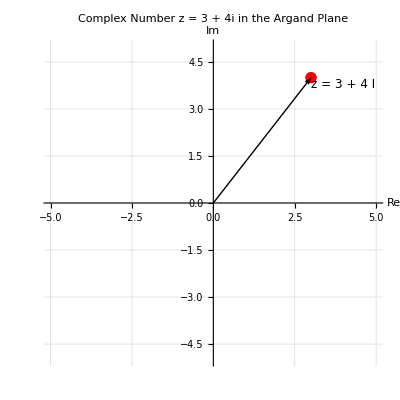

```mathematica
(*Define a complex number*)
z=3+4*I;

(*Visualize a single complex number in the Argand plane*)
argandPoint=ListPlot[{{Re[z],Im[z]}},PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-5,5},{-5,5}},AspectRatio->1,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{Arrow[{{0,0},{Re[z],Im[z]}}],Text[Style["z = "<>ToString[z],12],{Re[z],Im[z]},{-1,1}]},PlotLabel->"Complex Number z = 3 + 4i in the Argand Plane"]
```

### Polar Representation

A complex number can also be represented in polar form as , where:
	-  is the magnitude (or modulus) of the complex number
	-  is the argument (or phase) of the complex number
In Mathematica, we can convert between rectangular and polar forms:

```mathematica
(*Convert from rectangular to polar form*)
z=3+4*I;
r=Abs[z ];
theta=Arg[z];

(*Display in exponential form*)
polarForm=r*Exp[I*theta];
polarFormString=ToString[r]<>" e^("<>ToString[theta,InputForm]<>"i)";

(*Verify using Euler's formula*)
eulersFormula=r*(Cos[theta]+I*Sin[theta])
Simplify[eulersFormula-z]  (*Should be 0*)
```

3+4 ⅈ

0

### Visualizing Complex Functions

We can visualize how complex functions transform the Argand plane:

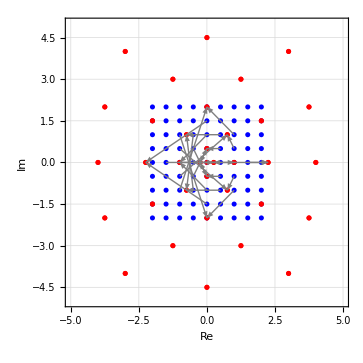

```mathematica
(*Create a grid of complex numbers*)
gridPoints=Table[a+b*I,{a,-2,2,0.5},{b,-2,2,0.5}];
gridPoints=Flatten[gridPoints];

(*Define a complex function*)
f[z_]:=z^2;

(*Apply the function to each point*)
transformedPoints=f/@gridPoints;

(*Visualize the transformation*)
transformation=Graphics[{
(*Original grid points*)
Blue,PointSize[0.01],Point[{Re[#],Im[#]}&/@gridPoints],
(*Transformed grid points*)
Red,PointSize[0.01],Point[{Re[#],Im[#]}&/@transformedPoints],
(*Connect corresponding points with arrows*)
Gray,Arrowheads[0.02],Arrow[{{Re[#],Im[#]},{Re[f[#]],Im[f[#]]}}]&/@Select[gridPoints,Abs[#]<=1.5&]
},
PlotRange->{{-5,5},{-5,5}},AspectRatio->1,Frame->True,FrameLabel->{{"Im",None},{"Re","Complex Function f(z) = z.b2"}},GridLines->Automatic]
```

Or more maturely we can use the built-in function in Mathematica:

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

### Complex Exponential and Trigonometric Functions

Using Euler' s identity, we can express trigonometric functions in terms of complex exponentials :

1/2 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ))

-1/2 ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ))

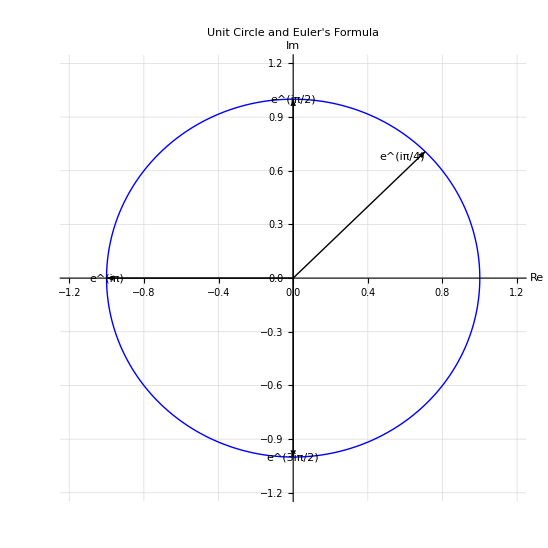

```mathematica
(*Euler's identity*)
eulerIdentity=Exp[I*θ]==Cos[θ]+I*Sin[θ];

(*Solving for cosine and sine*)
cosTheta=Simplify[(Exp[I*θ]+Exp[-I*θ])/2]
sinTheta=Simplify[(Exp[I*θ]-Exp[-I*θ])/(2*I)]

(*Visualizing the relationship with a unit circle*)
unitCircle=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue},PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{Arrow[{{0,0},{Cos[Pi/4],Sin[Pi/4]}}],Text["e^(iπ/4)",{Cos[Pi/4],Sin[Pi/4]},{1,1}],Arrow[{{0,0},{Cos[Pi/2],Sin[Pi/2]}}],Text["e^(iπ/2)",{Cos[Pi/2],Sin[Pi/2]},{0,1}],Arrow[{{0,0},{Cos[Pi],Sin[Pi]}}],Text["e^(iπ)",{Cos[Pi],Sin[Pi]},{-1,0}],Arrow[{{0,0},{Cos[3*Pi/2],Sin[3*Pi/2]}}],Text["e^(3iπ/2)",{Cos[3*Pi/2],Sin[3*Pi/2]},{0,-1}]},PlotLabel->"Unit Circle and Euler's Formula"]
```

### De Moivre’s Formula

De Moivre’s formula provides a simple way to compute powers of complex numbers:

5^n (ⅇ^(ⅈ θ))^n==5^n ⅇ^(ⅈ n θ)

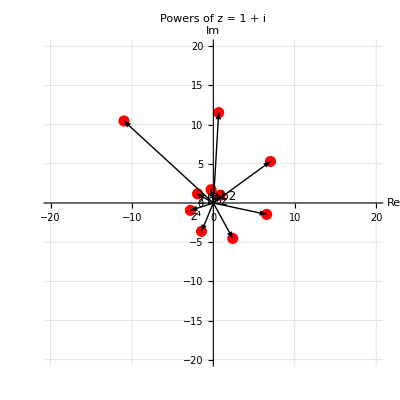

```mathematica
(*De Moivre's formula:(r e^(iθ))^n=r^n e^(inθ)*)
deMoivreFormula=Simplify[(r*Exp[I*θ])^n==r^n*Exp[I*n*θ]]

(*Example:Computing powers of complex numbers*)
z=0.85+I;  (*r=√2,θ=π/4*)
powers=Table[z^k,{k,1,10}];

(*Show the powers on the Argand plane*)
powerPlot=ListPlot[{Re[#],Im[#]}&/@powers,PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-20,20},{-20,20}},AspectRatio->1,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{Arrow[{{0,0},{Re[#],Im[#]}}]&/@powers,Text[Style["z",12],{Re[z],Im[z]},{-1,1}],Text[Style["z.b2",12],{Re[z^2],Im[z^2]},{-1,1}],Text[Style["z.b3",12],{Re[z^3],Im[z^3]},{-1,1}],Text[Style["z⁴",12],{Re[z^4],Im[z^4]},{-1,1}]},PlotLabel->"Powers of z = 1 + i"]
```

### Complex Roots

We can find the n - th roots of a complex number and visualize them :

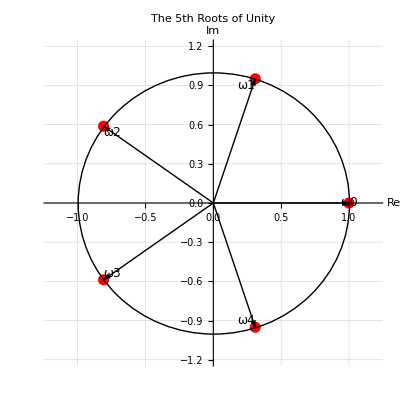

```mathematica
(*Find nth roots of a complex number*)
findRoots[z_,n_]:=Table[Abs[z]^(1/n)*Exp[I*(Arg[z]+2*Pi*k)/n],{k,0,n-1}]

(*Example:Find the 5th roots of 1*)
roots=findRoots[1,5];

(*Visualize the roots*)
rootsPlot=ListPlot[{Re[#],Im[#]}&/@roots,PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{Circle[],(*Unit circle*)Arrow[{{0,0},{Re[#],Im[#]}}]&/@roots,MapIndexed[Text[Style["ω"<>ToString[First[#2]-1],12],{Re[#1],Im[#1]},{Sign[Re[#1]],Sign[Im[#1]]}]&,roots]},PlotLabel->"The 5th Roots of Unity"]
```

### Interactive Exploration of Complex Numbers

```mathematica
Manipulate[
Column[
{
Graphics[
{
(*Argand plane*)
Gray,Line[{{-3,0},{3,0}}],Line[{{0,-3},{0,3}}],Text["Re",{3.1,0}],Text["Im",{0,3.1}],
(*Vector representation*)
{
Blue,Arrow[{{0,0},{a,b}}]},Text[Style["z = "<>ToString[a+b*I],12],{a,b},{-1,1}],
(*Polar form information*)
{Red,Circle[{0,0},Sqrt[a^2+b^2],{0,ArcTan[a,b]}]},{Red,Dashed,Line[{{0,0},{Sqrt[a^2+b^2],0}}]},Text[Style["r = "<>ToString[Round[Sqrt[a^2+b^2],0.01]],10],{Sqrt[a^2+b^2]/2,-0.2}],Text[Style["θ = "<>ToString[Round[ArcTan[a,b],0.01]],10],{a/2,b/2},{0,-1}]
},
PlotRange->{{-3,3},{-3,3}},AspectRatio->1,GridLines->Automatic
],
Style["Complex Number: "<>ToString[a+b*I],Bold],"Rectangular form: "<>ToString[a]<>" + "<>ToString[b]<>"i","Polar form: "<>ToString[Round[Sqrt[a^2+b^2],0.01]]<>" e^("<>ToString[Round[ArcTan[a,b],0.01]]<>"i)"}
],{{a,1},-3,3,0.1,Appearance->"Labeled"},{{b,1},-3,3,0.1,Appearance->"Labeled"},ControlPlacement->Right
]
```

```mathematica
TextCell["This gives us the L.b2-norm of the sine function on [0, π]. Now, the distance between two vectors/functions is defined as:

d(f, g) = ‖f - g‖

Try computing distance between Sin[x] and Cos[x]:","Text"]
```

This gives us the L.b2-norm of the sine function on [0, π]. Now, the distance between two vectors/functions is defined as:

d(f, g) = ‖f - g‖

Try computing distance between Sin[x] and Cos[x]:

## Vector Spaces

## Lists

Suppose  is a nonnegative integer. A list of length  is an ordered collection of  elements. Two lists are equal if and only if they have the same length and the same elements in the same order (notice the difference between lists and sets).

Lists are often written as elements separated by commas and surrounded by parentheses. In Mathematica however, we use curly brackets to show lists:

```mathematica
A = {1,2,3,4};
```

### Coordinate

is the set of all lists of length  of elements of .

```mathematica
F[A_,n_]:= Tuples[A, n];
F[A,2]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4}}

If  be the real numbers for  we get the usual  and . We can also define  to be the set of complex numbers, thus creating a complex coordinate.

#### Addition

Addition in  is defined by adding corresponding coordinates:

```mathematica
X = F[A,2];
X[[1]] + X[[2]] == {X[[1]][[1]]+X[[2]][[1]],X[[1]][[2]]+X[[2]][[2]]}
```

True

It is obvious to show that this definition of sum is commutative. Do it here as an exercise. Also one can define the additive inverse of any element of  by negative sign as:

```mathematica
Fn =Flatten[ {Tuples[A,2] , Tuples[-A,2]},1 ]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{-1,-1},{-1,-2},{-1,-3},{-1,-4},{-2,-1},{-2,-2},{-2,-3},{-2,-4},{-3,-1},{-3,-2},{-3,-3},{-3,-4},{-4,-1},{-4,-2},{-4,-3},{-4,-4}}

#### Scalar Multiplication

Having dealt with addition in , we now turn to multiplication. We could define a multiplication in  in a similar fashion.

The product of a number  and a vector in  is computed by multiplying each coordinate of the vector by :

```mathematica
λ Fn[[1]]
```

{λ,λ}

Scalar multiplication has a nice geometric interpretation in . If  and , then  is a vector that points in the same direction as .

### Digression on Fields

A field is a set containing at least two distinct elements called  and  along with operations of addition and multiplication satisfying all properties below:

1. Commutativity
2. Associativity
3. Identities
4. Additive inverse
5. Multiplication inverse
6. distributive property

Thus  are fields, as is the set of rational numbers along with the usual operations of addition and multiplication.

## Vector Space

The motivation for the definition of a vector space comes from properties of addition and scalar multiplication in : Addition is commutative, associative and has an identity. Every element has an additive inverse. Scalar multiplication is associative. Scalar multiplication by  acts as expected. Addition and scalar multiplication are connected by distributive properties.

We will define a vector space to be a set  with an addition and a scalar multiplication on  that satisfy the properties above.

### Addition and Scalar Multiplication

An addition on set  is a function that assigns an element  to each pair of elements .

A scalar multiplication on a set  is a function that assigns an element  to each  and each .

### Definition of Vector Space

A vector space is a set  along with an addition on  and a scalar multiplication on  such that the following properties hold.

Commutativity: 
Associativity: 
Additive Identity:   such that .
Additive Inverse:.
Multiplicative Identity: 
Distributive properties: .

Note: Elements of a vector space are called vectors or points.

The scalar multiplication in a vector space depends on . But usually the choice of  is either clear from the context or irrelevant. Thus we often assume that  is  lurking in tha background without specifically mentioning it. With the usual operations of addition and scalar multiplication  is a vector space over , as you should verify.

## Subspaces

A subset  of  is called a subspace of  if  is also a vector space with the same additive identity, addition, and scalar multiplication as on .

### Sum of Subspaces

Suppose  are subspaces of . The sum of , denoted by , is the set of all possible sums of elements of . More precisely,

### Direct Sum

Suppose s are subspaces of .
	- The sum of subspaces  is called a direct sum if each element of the sum can be written in only one way as a sum , where . For direct sums we use the notation .

## Basis Vectors

### Definition

A list of vectors in a vector space that is small enough to be linearly independent and big enough so the linear combinations of the list fill up the vector space is called a basis of the vector space. We will see that every basis of a vector space has the same length, which will allow us to define the dimension of a vector space

A basis of , is a list of vectors in  that is linearly independent and spans .

### Linear Combination

A linear combination of a list  of vectors in , is a vector of the form  where .

### Span

The set of all linear combination of a list of vectors  in  is called the span of , denoted by . If span of a list of vectors equals , we say that the list spans . A vector space is called finite-dimensional if some list of vectors in it spans the space.

### Finite-Dimensional Vector Space

A vector space is called finite-dimensional if a finite set of vectors can span it. For example:

```mathematica
Fn
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{-1,-1},{-1,-2},{-1,-3},{-1,-4},{-2,-1},{-2,-2},{-2,-3},{-2,-4},{-3,-1},{-3,-2},{-3,-3},{-3,-4},{-4,-1},{-4,-2},{-4,-3},{-4,-4}}

Can be spanned by:

```mathematica
V1 = {1,0}
V2 = {0,1}
```

{1,0}

{0,1}

Because for each member we can find:

```mathematica
Flatten[Table[Solve[a V1 + b V2 == Fn[[i]]], {i, 1,Length[Fn]}], 1]
```

{{a→1,b→1},{a→1,b→2},{a→1,b→3},{a→1,b→4},{a→2,b→1},{a→2,b→2},{a→2,b→3},{a→2,b→4},{a→3,b→1},{a→3,b→2},{a→3,b→3},{a→3,b→4},{a→4,b→1},{a→4,b→2},{a→4,b→3},{a→4,b→4},{a→-1,b→-1},{a→-1,b→-2},{a→-1,b→-3},{a→-1,b→-4},{a→-2,b→-1},{a→-2,b→-2},{a→-2,b→-3},{a→-2,b→-4},{a→-3,b→-1},{a→-3,b→-2},{a→-3,b→-3},{a→-3,b→-4},{a→-4,b→-1},{a→-4,b→-2},{a→-4,b→-3},{a→-4,b→-4}}

An infinite-dimensional vector space can also be defined when one proves that the vector space is not finite-dimensional.

### Linear Independent

A set of vectors is called linearly independent when the equation below satisfies only if the coefficients of the vector are zero, namely:

```mathematica
Solve[a V1 + b V2==0]
```

{{a→0,b→0}}

So the vectors defined above are linearly independent.

### Criterion for Basis

A list  of vectors in  is a basis of  if and only if every  can be written uniquely in the form:  where . 
Every spanning list in a vector space can be reduced to a basis of the vector space. And every finite-dimensional vector space has at least one basis. Every linearly independent list extends to a basis (either it is a basis or by adding vectors to it we can make a basis from it). Any two bases of a finite-dimensional vector space have the same length. The dimension of a finite-dimensional vector space is the length of any basis of the vector space. We use the notation .

#### Linearly independent list of the right length is a basis.

Suppose  is a finite-dimensional vector space. Then every linearly independent list of vectors in  of length  is a basis of .

#### Spanning list of the right length is a basis

Suppose  is finite-dimensional. Then every spanning list of vectors in  of length  is a basis of .

## Linear Maps

## Introduction

So far our attention has focused on vector spaces. No one gets excited about vector spaces. The interesting part of linear algebra is the subject to which we now turn linear maps. 

We will frequently use the powerful fundamental theorem of linear maps, which states that the dimension of the domain of a linear map equals the dimension of the subspace that gets sent to 0 plus the dimension of the range. This will imply the striking result that a linear map from a finite-dimensional vector space to itself is one-to-one if and only if its range is the whole space. 

A major concept that we will introduce in this chapter is the matrix associated with a linear map and with a basis of the domain space and a basis of the target space. This correspondence between linear maps and matrices provides much insight into key aspects of linear algebra.

## Definition

A Linear Map from  to  is a function  with the following properties:
1. Additivity: 
2. Homogeneity: 

Note that for linear maps we often use the notation  as well as the usual function notation . 

The set of linear maps from  to  is denoted by . And the set of linear maps from a vector space  to itself is simply .

### Addition and Scalar Multiplication on

Suppose  and . The sum  and the product  are the linear maps from  to  defined by:

 and 
Because we took the trouble to define addition and scalar multiplication on , the next result should not be a surprise. 

With the operations of addition and scalar multiplication as defined above,  is a vector space.

### The Product of Linear Maps

If  and , then the product  is defined by:

note that the domain and range of functions are connected with each other.

## Fundamental Theorem of Linear Maps

Suppose  is a finite dimensional and . Then the range is finite dimensional and:

.

## Matrices

### Representing a Linear Map by a Matrix

We know that if  is a basis of  and  is linear, then the values of  determine the values of  on arbitrary vectors in .  Matrices provide an efficient method of recording the values of ’s in terms of a basis of .

Suppose  and  are nonnegative integers. An -by- matrix  is a rectangular array of elements of  with  rows and  columns:

```mathematica
A = ({{a11, a12, a13}, {a21, a22, a23}, {a31, a32, a33}})
```

{{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}

```mathematica
%//MatrixForm
```

(a11 | a12 | a13
a21 | a22 | a23
a31 | a32 | a33)

### Matrix of a Linear Map

Suppose  and  are a basis of  and  are a basis of . The matrix of  with respect to these bases are defined by:

### Addition and Scalar Multiplication of Matrices

The sum of two matrices of the same size is the matrix obtained by adding corresponding entries in the matrices:

```mathematica
A = {{1,1},{2,3}};
B = {{2,1},{3,4}};
A//MatrixForm
B//MatrixForm
A . B //MatrixForm
```

(1 | 1
2 | 3)

(2 | 1
3 | 4)

(5 | 5
13 | 14)

For scalar multiplication, one can use the same means of vector-scalar multiplication,

```mathematica
λ A
```

{{λ,λ},{2 λ,3 λ}}

I won’t go in anymore details about matrices but I gave some references at the end of this notebook.

## Matrix Factorization

Matrix factorization (or decomposition) refers to the process of expressing a matrix as a product of two or more matrices. These factorizations are extremely useful in numerical linear algebra, as they simplify complex operations, increase computational efficiency, and provide insights into the mathematical structure of the original matrix.

We’ll explore five fundamental matrix factorization techniques:

LU Decomposition

QR Factorization

LDL Decomposition

Singular Value Decomposition (SVD)

Low Rank Approximations

Each technique has specific applications and advantages depending on the problem at hand.

## LU Decomposition

decomposition factors a matrix  into the product of a lower triangular matrix  and an upper triangular matrix :

This decomposition is particularly useful for solving systems of linear equations, computing determinants, and inverting matrices.

For a square matrix , the  decomposition works by using Gaussian elimination to transform  into an upper triangular matrix , while keeping track of the elimination operations in a lower triangular matrix .
The process requires that  can be factorized without row exchanges (pivoting). If pivoting is needed, we get a slightly modified form: , where  is a permutation matrix.

```mathematica
(*Create a sample matrix*)
A={{1,3,2},{2,2,3},{3,4,4}};
MatrixForm[A]

(*Perform LU decomposition*)
{lu,p,c}=LUDecomposition[A];

L = LowerTriangularize[lu,-1]+IdentityMatrix[3];
U = UpperTriangularize[lu];
L//MatrixForm
U//MatrixForm
L.U//MatrixForm
Equal[A, L.U]
```

(1 | 3 | 2
2 | 2 | 3
3 | 4 | 4)

(1 | 0 | 0
2 | 1 | 0
3 | 5/4 | 1)

(1 | 3 | 2
0 | -4 | -1
0 | 0 | -3/4)

(1 | 3 | 2
2 | 2 | 3
3 | 4 | 4)

True

### Example: Solving Linear System with LU Decomposition

```mathematica
(*Define a linear system Ax=b*)
A={{4,3,2},{2,1,3},{3,4,1}};
b={13,12,19};

(*Perform LU decomposition*)
{lu,p,c}=LUDecomposition[A];
L =  LowerTriangularize[lu,-1]+IdentityMatrix[3];
U = UpperTriangularize[lu];
(*Solve the system using LU decomposition*)

x=Inverse[U].Inverse[L]. b

Print["Solution to the system Ax = b:"];
x

(*Verify the solution*)
Print["Verification: Ax = b?"];
A.x
b
Sort[A.x] == Sort[b] (* We have to sort to make sure we're treating it like a set not like a list.*)
```

{-66/13,94/13,69/13}

Solution to the system Ax = b:

{-66/13,94/13,69/13}

Verification: Ax = b?

{12,13,19}

{13,12,19}

True

### Visualization of LU Decomposition

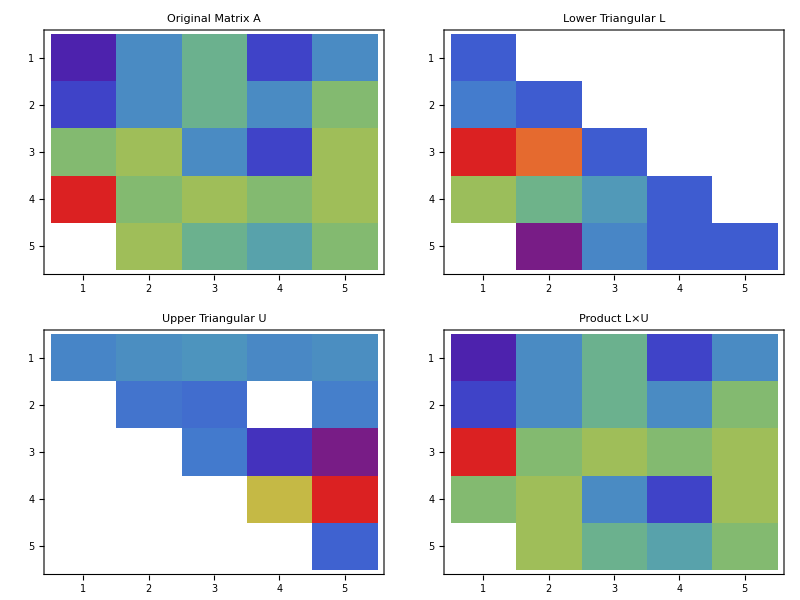

```mathematica
(*Create a function to visualize matrices*)visualizeMatrix[mat_,title_]:=ArrayPlot[mat,ColorRules->{0->White},ColorFunction->"Rainbow",Frame->True,FrameTicks->{Range[1,Length[mat]],Range[1,Length[mat[[1]]]]},PlotLabel->title]


A={
{1,4,6,2,4},
{2,4,6,4,7},
{7,8,4,2,8},
{14,7,8,7,8},
{0,8,6,5,7}
};
(*Perform LU decomposition*)
{lu,p,c}=LUDecomposition[A];

(*Extract L and U*)
L= LowerTriangularize[lu,-1]+IdentityMatrix[5];
U= UpperTriangularize[lu];
(*Visualize A,L,U,and L×U*)
Grid[{{visualizeMatrix[A,"Original Matrix A"],visualizeMatrix[L,"Lower Triangular L"]},{visualizeMatrix[U,"Upper Triangular U"],visualizeMatrix[L.U,"Product L×U"]}}]
```

## QR Factorization

factorization decomposes a matrix  into the product of an orthogonal matrix  and an upper triangular matrix :
.
This decomposition is particularly useful for solving least squares problems, computing eigenvalues, and orthogonalizing sets of vectors.

There are several methods for computing  decomposition including:

1. Gram-Schmidt orthogonalization
2. Householder reflections
3. Givens rotations

The  decomposition has the useful property that  (where  is the transpose of ), which simplifies many matrix operations.

```mathematica
(*Create a sample matrix*)
A={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[A]

(*Perform QR decomposition*)
{Q,R}=QRDecomposition[A];

(*Display Q and R*)
Print["Orthogonal matrix Q:"];
MatrixForm[Q]

Print["Upper triangular matrix R:"];
MatrixForm[R]

(*Verify decomposition*)
Print["Verification: Q×R equals original matrix A?"];
MatrixForm[A] ==MatrixForm[ConjugateTranspose[Q].R]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Orthogonal matrix Q:

(1/(√66) | 2 √(2/33) | 7/(√66)
3/(√11) | 1/(√11) | -1/(√11))

Upper triangular matrix R:

(√66 | 13 √(6/11) | 15 √(6/11)
0 | 3/(√11) | 6/(√11))

Verification: Q×R equals original matrix A?

True

### Example: Solving Least Squares Problem

{7/5,7/2}

Solution to the least squares problem:

{7/5,7/2}

{7/5,7/2}

Direct least squares solution:

{7/5,7/2}

√(21/5)

Residual norm: √(21/5)

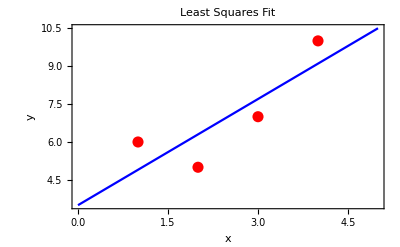

```mathematica
(*Create an overdetermined system*)
A={{1,1},{2,1},{3,1},{4,1}};
b={6,5,7,10};

(*QR decomposition approach to least squares*)
{Q,R}=QRDecomposition[A];
y=Q.b;
x=LinearSolve[R,y[[1;;Length[R]]]]

Print["Solution to the least squares problem:"];
x

(*Compare with direct least squares solution*)
lsqSolution=LinearSolve[Transpose[A].A,Transpose[A].b]
Print["Direct least squares solution:"];
lsqSolution

(*Calculate and display residual*)
residual=Norm[A.x-b]
Print["Residual norm: ",residual]

(*Visualization of the fit for a line y=mx+c*)
model[t_,{m_,c_}]:=m*t+c;
fitPlot=Show[ListPlot[Transpose[{A[[All,1]],b}],PlotStyle->{Red,PointSize[0.02]},PlotLabel->"Least Squares Fit"],Plot[model[t,x],{t,0,5},PlotStyle->Blue],Frame->True,PlotRange->All,FrameLabel->{"x","y"},PlotLegends->{"Data Points","Fitted Line"}]
```

### Visualization: QR Decomposition

```mathematica
(*Create a 3×2 matrix for visualization*)
A={{3,2,4},{1,4,5},{2,1,2}};

(*Perform QR decomposition*)
{Q,R}=QRDecomposition[A];

(*Create 3D vectors representing the columns of A and Q*)
aVectors=Transpose[A];
qVectors=Transpose[Q];

(*Visualization in 3D space*)
vectorPlot=Graphics3D[{{Red,Arrow[{{0,0,0},aVectors[[1]]}],Text["a_1",aVectors[[1]]+{0.2,0.2,0.2}]},{Red,Arrow[{{0,0,0},aVectors[[2]]}],Text["a_2",aVectors[[2]]+{0.2,0.2,0.2}]},{Blue,Arrow[{{0,0,0},qVectors[[1]]}],Text["q_1",qVectors[[1]]+{0.2,0.2,0.2}]},{Blue,Arrow[{{0,0,0},qVectors[[2]]}],Text["q_2",qVectors[[2]]+{0.2,0.2,0.2}]}},PlotRange->{{-1,5},{-1,5},{-1,5}},BoxRatios->{1,1,1},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"Columns of A (red) and Q (blue)"];

Show[vectorPlot]
```

-Graphics3D-

## LDL Decomposition and Positive Definite Matrices

decomposition is a variant of  decomposition for symmetric matrices where:

Here,  is a lower triangular matrix with 1’s on the diagonal, and  is a diagonal matrix.

For a symmetric matrix , the  decomposition provides a more efficient and numerically stable alternative to Cholesky decomposition, especially when  is not guaranteed to be positive definite.

If  is positive definite, we can further simplify to the Cholesky decomposition, where A = .

```mathematica
(*Create a symmetric matrix*)
A={{4,2,2},{2,4,4},{2,4,4}};
MatrixForm[A]

(*Verify that A is symmetric*)
Print["Is A symmetric? ",A==Transpose[A]]

(*Perform LDL decomposition manually*)
n=Length[A];
L=IdentityMatrix[n];
Diag=ConstantArray[0,n]

For[j=1,j<=n,j++,(*Calculate diagonal element of D*)Diag[[j]]=A[[j,j]]-Sum[L[[j,k]]^2*Diag[[k]],{k,1,j-1}];
(*Calculate elements of L below the diagonal*)For[i=j+1,i<=n,i++,L[[i,j]]=(A[[i,j]]-Sum[L[[i,k]]*L[[j,k]]*Diag[[k]],{k,1,j-1}])/Diag[[j]];]]

(*Create diagonal matrix from D*)
Dmat=DiagonalMatrix[Diag];

(*Display L and D*)
Print["Lower triangular matrix L:"];
MatrixForm[L]

Print["Diagonal matrix D:"];
MatrixForm[Dmat]

(*Verify decomposition*)
Print["Verification: L×D×L^T equals original matrix A?"];
MatrixForm[L.Dmat.Transpose[L]]== MatrixForm[A]
```

(4 | 2 | 2
2 | 4 | 4
2 | 4 | 4)

Is A symmetric? True

{0,0,0}

Lower triangular matrix L:

(1 | 0 | 0
1/2 | 1 | 0
1/2 | 1 | 1)

Diagonal matrix D:

(4 | 0 | 0
0 | 3 | 0
0 | 0 | 0)

Verification: L×D×L^T equals original matrix A?

True

### Positive Definite Matrices and Cholesky Decomposition

```mathematica
(*Check if A is positive definite*)
eigenvalues=Eigenvalues[A];
Print["Eigenvalues of A: ",eigenvalues];
Print["Is A positive definite? ",And@@(eigenvalues>0)]

(*If A is positive definite,we can use Cholesky decomposition*)
If[And@@(eigenvalues>0),(*Perform Cholesky decomposition*)L=CholeskyDecomposition[A];
Print["Cholesky factor L:"];
MatrixForm[L];
(*Verify Cholesky decomposition*)Print["Verification: L×L^T equals original matrix A?"];
MatrixForm[L.Transpose[L]];
MatrixForm[A];
Equal[L.Transpose[L],A],Print["Matrix is not positive definite, cannot perform Cholesky decomposition"]]
```

Eigenvalues of A: {2 (3+√3),2 (3-√3),0}

Is A positive definite? {2 (3+√3),2 (3-√3),0}&&0

If[{2 (3+√3),2 (3-√3),0}&&0,L=CholeskyDecomposition[A];Print[Cholesky factor L:];L;Print[Verification: L×L^T equals original matrix A?];L.Transpose[L];A;L.Transpose[L]==A,Print[Matrix is not positive definite, cannot perform Cholesky decomposition]]

### Visualization: Positive Definite Matrices and Ellipsoids

Eigenvalues: {2+√2,2,2-√2}

Is A positive definite? {2+√2,2,2-√2}&&0

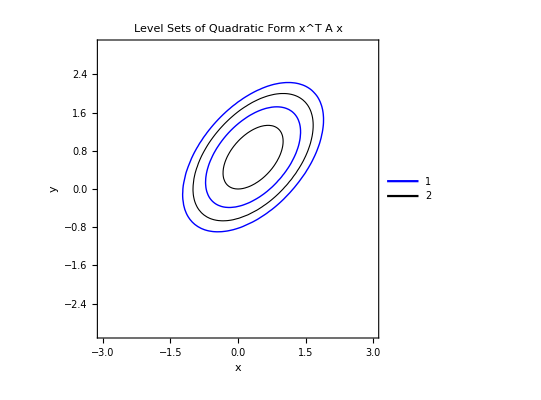

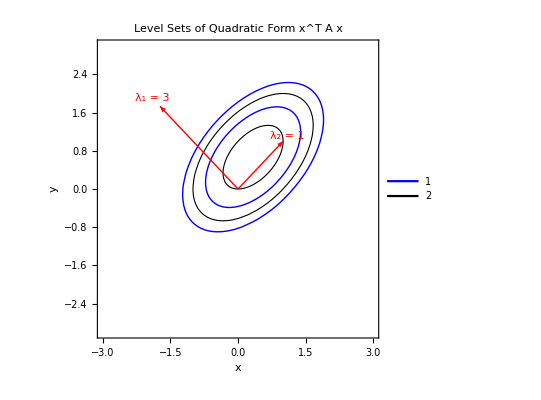

```mathematica
(*Create a positive definite matrix*)A={{2,-1,0},{-1,2,-1},{0,-1,2}};

(*Check positive definiteness*)
eigenvalues=Eigenvalues[A];
Print["Eigenvalues: ",eigenvalues];
Print["Is A positive definite? ",And@@(eigenvalues>0)]

(*Create a quadratic form function*)
quadraticForm[x_,mat_]:=x.mat.x

(*Visualize a 2D ellipse corresponding to the quadratic form*)
ellipsePlot=ContourPlot[quadraticForm[{x,y,1},A],{x,-3,3},{y,-3,3},Contours->{1,2,3,4,5},ContourShading->None,ContourStyle->{Blue,Thickness[0.002]},PlotLabel->"Level Sets of Quadratic Form x^T A x",FrameLabel->{"x","y"},PlotTheme->"Detailed"]

(*Visualize the eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[A[[1;;2,1;;2]]];
eigenvectorPlot=Graphics[{Red,Arrow[{{0,0},vecs[[1]]*Sqrt[vals[[1]]]}],Arrow[{{0,0},vecs[[2]]*Sqrt[vals[[2]]]}],Text["λ₁ = "<>ToString[vals[[1]]],vecs[[1]]*Sqrt[vals[[1]]]*1.1],Text["λ₂ = "<>ToString[vals[[2]]],vecs[[2]]*Sqrt[vals[[2]]]*1.1]}];

Show[ellipsePlot,eigenvectorPlot]
```

## Singular Value Decomposition

Singular Value Decomposition (SVD) is one of the most important matrix factorizations, expressing any m×n matrix A as:

where:
	-  is an  orthogonal matrix containing the left singular vectors
	-  is an  diagonal matrix containing singular values .
	-  is the transpose of an  orthogonal matrix  containing the right singular vectors.
	
	SVD reveals fundamental properties of a linear transformation represented by matrix :
	- The singular values indicate the “stretching” in each direction.
	- The left singular vectors (columns of ) form an orthonormal basis for the column space.
	- The right singular vectors (columns of ) form an orthonormal basis for the row space.

```mathematica
(*Create a sample matrix*)
A={{3,2,2},{2,3,-2}};
MatrixForm[A]

(*Perform SVD*)
{U,S,V}=SingularValueDecomposition[A];

(*Display the components*)
Print["Left singular vectors (U):"];
MatrixForm[U]

Print["Singular values (Σ):"];
MatrixForm[S]

Print["Right singular vectors (V):"];
MatrixForm[V]

(*Verify decomposition*)
Print["Verification: U×Σ×V^T equals original matrix A?"];
MatrixForm[U.S.Transpose[V]]
MatrixForm[A]
```

(3 | 2 | 2
2 | 3 | -2)

Left singular vectors (U):

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

Singular values (Σ):

(5 | 0 | 0
0 | 3 | 0)

Right singular vectors (V):

(1/(√2) | -1/(3 √2) | -2/3
1/(√2) | 1/(3 √2) | 2/3
0 | -(2 √2)/3 | 1/3)

Verification: U×Σ×V^T equals original matrix A?

(3 | 2 | 2
2 | 3 | -2)

(3 | 2 | 2
2 | 3 | -2)

### Example: Computing Pseudoinverse

```mathematica
(*Create a non-square matrix*)
A={{1,2},{3,4},{5,6}};
MatrixForm[A]

(*Compute pseudoinverse using SVD*)
{U,S,V}=SingularValueDecomposition[A];

(*Replace non-zero singular values with their reciprocals*)
SInv=S;
For[i=1,i<=Min[Dimensions[S]],i++,If[S[[i,i]]>10^-10,SInv[[i,i]]=1/S[[i,i]],SInv[[i,i]]=0]]

(*Calculate pseudoinverse:A⁺=V·Σ⁺·U^T*)
Aplus=V.Transpose[SInv].Transpose[U];
Print["Pseudoinverse of A:"];
MatrixForm[Aplus]

(*Verify the pseudoinverse properties*)
Print["Verification: A·A⁺·A = A?"];
MatrixForm[A.Aplus.A]
MatrixForm[A]
```

(1 | 2
3 | 4
5 | 6)

Pseudoinverse of A:

(((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))) | ((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))) | ((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))
(2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))) | (4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))) | (6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))

Verification: A·A⁺·A = A?

(((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+5 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))) | 2 (((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+4 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+6 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))+2 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))
4 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (4 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+5 (4 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))) | 2 (4 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+4 (4 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+6 (4 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))
6 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+3 (6 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+5 (6 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))) | 2 (6 ((2+1/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (2+1/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (8/11+12/(11 (91+√8185))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+4 (6 ((4+3/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (4+3/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (4+3 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2)))))+6 (6 ((6+5/88 (-21+√8185)) √(2/((91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))+5 (((-21+√8185) (6+5/88 (-21+√8185)))/(44 √(2 (91+√8185) (1+(-21+√8185)^2/7744) ((2+1/88 (-21+√8185))^2+(4+3/88 (-21+√8185))^2+(6+5/88 (-21+√8185))^2)))+1/4 (-14/11+12/(11 (91+√8185))) (6+5 (-14/11+12/(11 (91+√8185)))) √((91+√8185)/(3 (1+(-14/11+12/(11 (91+√8185)))^2) ((8/11+12/(11 (91+√8185)))^2+(4+3 (-14/11+12/(11 (91+√8185))))^2+(6+5 (-14/11+12/(11 (91+√8185))))^2))))))

(1 | 2
3 | 4
5 | 6)

### Visualization: Geometric Interpretation of SVD

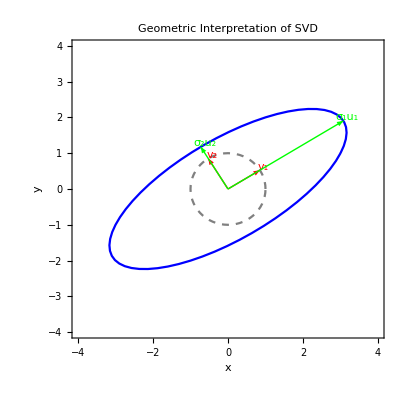

-Graphics-

```mathematica
(*Create a 2×2 matrix for visualization*)
A={{3,1},{1,2}};

(*Perform SVD*)
{U,S,V}=SingularValueDecomposition[A];
s1=S[[1,1]];
s2=S[[2,2]];

(*Define unit circle and its image under A*)
unitCircle=Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/30}];
transformedCircle=Map[A.#&,unitCircle];

(*Define vectors for visualization*)
v1=V[[All,1]];
v2=V[[All,2]];
u1=U[[All,1]];
u2=U[[All,2]];

(*Create the visualization*)
svdPlot=Show[(*Unit circle*)ListLinePlot[unitCircle,AspectRatio->1,PlotStyle->{Gray,Dashed}],(*Image of unit circle under A*)ListLinePlot[transformedCircle,PlotStyle->{Blue}],(*Right singular vectors*)Graphics[{{Red,Arrow[{{0,0},v1}],Text["v₁",v1+{0.1,0.1}]},{Red,Arrow[{{0,0},v2}],Text["v₂",v2+{0.1,0.1}]}}],(*Left singular vectors scaled by singular values*)Graphics[{{Green,Arrow[{{0,0},s1*u1}],Text["σ₁u₁",s1*u1+{0.1,0.1}]},{Green,Arrow[{{0,0},s2*u2}],Text["σ₂u₂",s2*u2+{0.1,0.1}]}}],PlotRange->{{-4,4},{-4,4}},PlotLabel->"Geometric Interpretation of SVD",Frame->True,FrameLabel->{"x","y"}]

svdPlot
```

## Low Rand Approximations

Low rank approximations use truncated SVD to represent a matrix with fewer parameters while minimizing the approximation error.

The Eckart-Young theorem states that the best rank-k approximation to a matrix A in terms of the Frobenius norm is given by:

.

Where:
	-  contains the first  columns of .
	-  is the  top-left submatrix of .
	-  contains the first  columns of .

The approximation error is

```mathematica
(*Create a sample matrix*)
A={{3,1,1,1},{1,3,1,1},{1,1,3,1},{1,1,1,3}};
MatrixForm[A]

(*Perform SVD*)
{U,S,V}=SingularValueDecomposition[A];

(*Display singular values*)
singularValues=Table[S[[i,i]],{i,1,Min[Dimensions[S]]}];
Print["Singular values: ",singularValues];

(*Function to compute rank-k approximation*)
rankKApproximation[U_,S_,V_,k_]:=U[[All,1;;k]].S[[1;;k,1;;k]].Transpose[V[[All,1;;k]]];

(*Compute different rank approximations*)
A1=rankKApproximation[U,S,V,1];
A2=rankKApproximation[U,S,V,2];
A3=rankKApproximation[U,S,V,3];

(*Display the approximations*)
Print["Rank-1 approximation:"];
MatrixForm[A1]

Print["Rank-2 approximation:"];
MatrixForm[A2]

Print["Rank-3 approximation:"];
MatrixForm[A3]

(*Calculate approximation errors*)
error1=Norm[A-A1,"Frobenius"];
error2=Norm[A-A2,"Frobenius"];
error3=Norm[A-A3,"Frobenius"];

Print["Approximation errors:"];
Print["Error for rank-1: ",error1];
Print["Error for rank-2: ",error2];
Print["Error for rank-3: ",error3];

(*Verify that the error matches the discarded singular values*)
theoreticalError1=Sqrt[Total[singularValues[[2;;]]^2]];
theoreticalError2=Sqrt[Total[singularValues[[3;;]]^2]];
theoreticalError3=Sqrt[Total[singularValues[[4;;]]^2]];

Print["Do errors match theoretical predictions?"];
Print["Rank-1: ",Abs[error1-theoreticalError1]<10^-10];
Print["Rank-2: ",Abs[error2-theoreticalError2]<10^-10];
Print["Rank-3: ",Abs[error3-theoreticalError3]<10^-10];
```

(3 | 1 | 1 | 1
1 | 3 | 1 | 1
1 | 1 | 3 | 1
1 | 1 | 1 | 3)

Singular values: {6,2,2,2}

Rank-1 approximation:

(3/2 | 3/2 | 3/2 | 3/2
3/2 | 3/2 | 3/2 | 3/2
3/2 | 3/2 | 3/2 | 3/2
3/2 | 3/2 | 3/2 | 3/2)

Rank-2 approximation:

(5/2 | 3/2 | 3/2 | 1/2
3/2 | 3/2 | 3/2 | 3/2
3/2 | 3/2 | 3/2 | 3/2
1/2 | 3/2 | 3/2 | 5/2)

Rank-3 approximation:

(17/6 | 3/2 | 5/6 | 5/6
3/2 | 3/2 | 3/2 | 3/2
5/6 | 3/2 | 17/6 | 5/6
5/6 | 3/2 | 5/6 | 17/6)

Approximation errors:

Error for rank-1: 2 √3

Error for rank-2: 2 √2

Error for rank-3: 2

Do errors match theoretical predictions?

Rank-1: True

Rank-2: True

Rank-3: True

### Visualization: Energy Captured in Low-Rank Approximations

Number of singular values needed for:

90% energy: 3

95% energy: 4

99% energy: 4

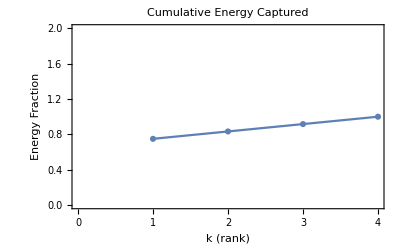

```mathematica
(*Calculate the "energy" captured by each singular value*)
totalEnergy=Total[singularValues^2];
energyVector=Accumulate[singularValues^2]/totalEnergy;

(*Plot the cumulative energy*)
energyPlot=ListPlot[energyVector,PlotMarkers->Automatic,Joined->True,PlotRange->{0,2},PlotLabel->"Cumulative Energy Captured",AxesLabel->{"k (rank)","Energy Fraction"},GridLines->{ranks,None},PlotTheme->"Detailed"];

(*Find how many singular values needed for 90%,95%,99% energy*)
k90=FirstPosition[energyVector,x_/;x>=0.9][[1]];
k95=FirstPosition[energyVector,x_/;x>=0.95][[1]];
k99=FirstPosition[energyVector,x_/;x>=0.99][[1]];

Print["Number of singular values needed for:"];
Print["90% energy: ",k90];
Print["95% energy: ",k95];
Print["99% energy: ",k99];

energyPlot
```

## Eigenvalues, Eigenvectors and Spectral Theorems

## Definition

Eigenvalues and eigenvectors are fundamental concepts in linear algebra that provide deep insights into the behavior of linear transformations.

### Basic Definition

For a square matrix , a non-zero vector  is an eigen-vector of  if there exists a scalar  (lambda) such that . 

The scalar  is called the eigen value corresponding to the eigenvector . This equation tells us that when  acts on , it only changes its magnitude by a factor of , not its direction.

### Characteristic Polynomial and Eigenvalue Computation

Eigen values can be found by solving the characteristic equation:

```mathematica
(*Define a sample matrix*)A={{4,2},{1,3}};
MatrixForm[A]

(*Compute the characteristic polynomial*)
charPoly=CharacteristicPolynomial[A,λ]
Print["Characteristic polynomial: ",charPoly]

(*Find the eigenvalues by solving the characteristic equation*)
eigenvalues=Solve[charPoly==0,λ]
Print["Eigenvalues: ",eigenvalues]

(*Use built-in function to find eigenvalues*)
eigvals=Eigenvalues[A]
Print["Eigenvalues (using built-in function): ",eigvals]
```

(4 | 2
1 | 3)

10-7 λ+λ^2

Characteristic polynomial: 10-7 λ+λ^2

{{λ→2},{λ→5}}

Eigenvalues: {{λ→2},{λ→5}}

{5,2}

Eigenvalues (using built-in function): {5,2}

This equation produces the characteristic polynomial, whose roots are the eigenvalues of .

### Computing Eigenvectors

Once we know an eigenvalue, we can find the corresponding eigenvector  by solving:

```mathematica
(*Find eigenvectors for each eigenvalue*)
eigenvectors={};
For[i=1,i<=Length[eigvals],i++,(*Set up the homogeneous system (A-λI)v=0*)λ=eigvals[[i]];
system=A-λ*IdentityMatrix[Length[A]];
(*Solve the homogeneous system*)solution=NullSpace[system];
AppendTo[eigenvectors,solution[[1]]];]

(*Display eigenvectors*)
Print["Eigenvectors:"];
Do[Print["For eigenvalue λ = ",eigvals[[i]],": ",eigenvectors[[i]]],{i,1,Length[eigvals]}]

(*Use built-in function to compute eigenvectors*)
{vals,vecs}=Eigensystem[A];
Print["Eigenvalues and eigenvectors (using built-in function):"];
Do[Print["λ = ",vals[[i]],", v = ",vecs[[i]]],{i,1,Length[vals]}]

(*Verify the eigenvector equation A·v=λ·v*)
Print["Verification of A·v = λ·v:"];
Do[v=vecs[[i]];
λ=vals[[i]];
Print["For eigenpair ",i,":",MatrixForm[A.v]," ≈ ",MatrixForm[λ*v]],{i,1,Length[vals]}]
```

Eigenvectors:

For eigenvalue λ = 5: {2,1}

For eigenvalue λ = 2: {-1,1}

Eigenvalues and eigenvectors (using built-in function):

λ = 5, v = {2,1}

λ = 2, v = {-1,1}

Verification of A·v = λ·v:

For eigenpair 1:(10
5) ≈ (10
5)

For eigenpair 2:(-2
2) ≈ (-2
2)

### Properties of Eigenvalues and Eigenvectors

Several important properties related to eigenvalues and eigenvectors:

The trace of  equals the sum of its eigenvalues

```mathematica
Print["Trace of A: ",Tr[A]];
Print["Sum of eigenvalues: ",Total[eigvals]];
```

Trace of A: 7

Sum of eigenvalues: 7

The determinant of  equals the product of its eigenvalues

```mathematica
Print["Determinant of A: ",Det[A]];
Print["Product of eigenvalues: ",Times@@eigvals];
```

Determinant of A: 10

Product of eigenvalues: 10

is invertible if and only if all its eigenvalues are non-zero

Similar matrices have the same eigenvalues

```mathematica
P={{2,1},{1,1}};
Pinv=Inverse[P];
B=P.A.Pinv;

Print["Similar matrix B = P·A·P⁻.b9:"];
MatrixForm[B]

Print["Eigenvalues of B: ",Eigenvalues[B]];
Print["Eigenvalues of A: ",eigvals];
```

Similar matrix B = P·A·P⁻.b9:

(2 | 5
0 | 5)

Eigenvalues of B: {5,2}

Eigenvalues of A: {5,2}

### Visualizing Eigenvectors and Eigenvalues in 2D

For a  matrix, we can visualize how the linear transformation affects vectors in the plane, highlighting the special role of eigenvectors.

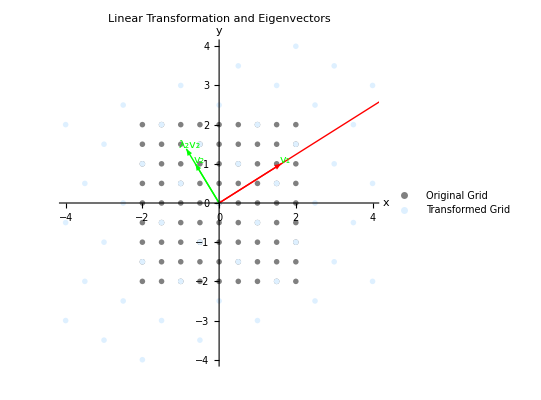

```mathematica
(*Create a visualization of eigenvectors and the transformation*)
A={{3,1},{1,2}};
{vals,vecs}=Eigensystem[A];

(*Create a grid of points*)
gridPoints=Flatten[Table[{i,j},{i,-2,2,0.5},{j,-2,2,0.5}],1];
transformedGrid=Map[A.#&,gridPoints];

(*Define the eigenvectors and their images*)
ev1=vecs[[1]];
ev2=vecs[[2]];
λ1=vals[[1]];
λ2=vals[[2]];

(*Create the visualization*)
eigenvectorPlot=Show[(*Draw the grid and its transformation*)ListPlot[{gridPoints,transformedGrid},PlotStyle->{{Gray,PointSize[0.01]},{LightBlue,PointSize[0.01]}},PlotLegends->{"Original Grid","Transformed Grid"}],(*Draw the eigenvectors and their transformations*)Graphics[{Red,Arrow[{{0,0},ev1}],Arrow[{{0,0},λ1*ev1}],Green,Arrow[{{0,0},ev2}],Arrow[{{0,0},λ2*ev2}],Text["v₁",ev1+{0.1,0.1}],Text["λ₁v₁",λ1*ev1+{0.1,0.1}],Text["v₂",ev2+{0.1,0.1}],Text["λ₂v₂",λ2*ev2+{0.1,0.1}]}],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->"Linear Transformation and Eigenvectors",AxesLabel->{"x","y"}];

eigenvectorPlot
```

## The Spectral Theorem for Symmetric Matrices

The spectral theorem is a fundamental result that provides a canonical form for certain classes of matrices.

### Statement of the Spectral Theorem

For a symmetric matrix , the spectral theorem states that.

All eigenvalues of  are real numbers.

Eigenvectors corresponding to distinct eigenvalues are orthogonal.

can be diagonalized by an orthogonal matrix , where  is a diagonal matrix containing the eigenvalues of .

### Verification of the Spectral Theorem

```mathematica
(*Create a symmetric matrix*)
A={{1,-1},{-1,1}}
MatrixForm[A]

(*Verify that A is symmetric*)
Print["Is A symmetric? ",A==Transpose[A]]

(*Find eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[A];
Print["Eigenvalues: ",vals];

(*Check that eigenvalues are real*)
Print["Are all eigenvalues real? ",And@@(Im[#]==0&/@vals)]

(*Normalize eigenvectors*)
normVecs=Map[Normalize,vecs];

(*Check orthogonality of eigenvectors*)
Print["Dot products between eigenvectors:"];
Table[normVecs[[i]].normVecs[[j]],{i,1,Length[normVecs]},{j,1,Length[normVecs]}]//MatrixForm

(*Construct the orthogonal matrix Q*)
Q=Transpose[normVecs];
Print["Orthogonal matrix Q:"];
MatrixForm[Q]

(*Verify that Q is orthogonal:Q^T·Q=I*)
Print["Q^T·Q = "];
MatrixForm[Transpose[Q].Q]

(*Construct the diagonal matrix D*)
Diag=DiagonalMatrix[vals];
Print["Diagonal matrix D:"];
MatrixForm[Diag]

(*Verify the spectral decomposition:A=Q·D·Q^T*)
Print["Q·D·Q^T = "];
MatrixForm[Q.Diag.Transpose[Q]]

Print["Original matrix A:"];
MatrixForm[A]

Print["Is A = Q·D·Q^T? ",And@@Flatten[Table[Abs[A[[i,j]]-(Q.Diag.Transpose[Q])[[i,j]]]<10^-10,{i,1,Length[A]},{j,1,Length[A]}]]]
```

{{1,-1},{-1,1}}

(1 | -1
-1 | 1)

Is A symmetric? True

Eigenvalues: {2,0}

Are all eigenvalues real? True

Dot products between eigenvectors:

(1 | 0
0 | 1)

Orthogonal matrix Q:

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

Q^T·Q =

(1 | 0
0 | 1)

Diagonal matrix D:

(2 | 0
0 | 0)

Q·D·Q^T =

(1 | -1
-1 | 1)

Original matrix A:

(1 | -1
-1 | 1)

Is A = Q·D·Q^T? True

### Spectral Decomposition

The spectral decomposition expresses a symmetric matrix  as:
, where  are the eigenvalues and  are the corresponding normalized eigenvectors.

```mathematica
(*Compute the spectral decomposition explicitly*)
A={{1,-1},{-1,1}};
{vals,vecs}=Eigensystem[A];
normVecs=Map[Normalize,vecs];

(*Construct the spectral decomposition*)
spectralSum=Sum[vals[[i]]*KroneckerProduct[normVecs[[i]],normVecs[[i]]],{i,1,Length[vals]}];

Print["Spectral decomposition:"];
MatrixForm[spectralSum]

Print["Original matrix:"];
MatrixForm[A]

Print["Difference (should be approximately zero):"];
MatrixForm[A-spectralSum]//FullSimplify
```

Spectral decomposition:

(1 | -1
-1 | 1)

Original matrix:

(1 | -1
-1 | 1)

Difference (should be approximately zero):

(0 | 0
0 | 0)

### Visualizing the Spectral Theorem in 2D and 3D

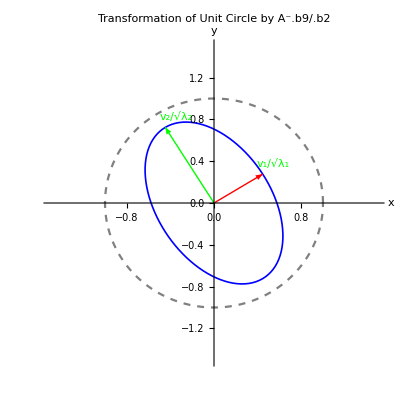

-Graphics3D-

```mathematica
(*Visualize spectral theorem in 2D-Ellipse axes aligned with eigenvectors*)
A={{3,1},{1,2}};
{vals,vecs}=Eigensystem[A];
normVecs=Map[Normalize,vecs];

(*Define an ellipse using the eigenvectors and eigenvalues*)
ellipsePoints=Table[Sqrt[1/vals[[1]]]*normVecs[[1]]*Cos[t]+Sqrt[1/vals[[2]]]*normVecs[[2]]*Sin[t],{t,0,2Pi,Pi/50}];

(*Create visualization*)
spectralEllipsePlot=Show[(*Draw the ellipse*)ListLinePlot[ellipsePoints,PlotStyle->{Blue,Thickness[0.003]}],(*Draw the eigenvectors scaled by eigenvalue*)Graphics[{Red,Arrow[{{0,0},Sqrt[1/vals[[1]]]*normVecs[[1]]}],Green,Arrow[{{0,0},Sqrt[1/vals[[2]]]*normVecs[[2]]}],Text["v₁/√λ₁",Sqrt[1/vals[[1]]]*normVecs[[1]]+{0.1,0.1}],Text["v₂/√λ₂",Sqrt[1/vals[[2]]]*normVecs[[2]]+{0.1,0.1}]}],(*Draw the unit circle for reference*)ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->{Gray,Dashed}],PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1,PlotLabel->"Transformation of Unit Circle by A⁻.b9/.b2",AxesLabel->{"x","y"}]

(*Visualize in 3D-Eigenvectors of a 3×3 symmetric matrix*)
A3D={{3,1,0},{1,2,0.5},{0,0.5,2}};
{vals3D,vecs3D}=Eigensystem[A3D];
normVecs3D=Map[Normalize,vecs3D];

(*Create a 3D ellipsoid*)
ellipsoid3D=Graphics3D[{Opacity[0.5],Ellipsoid[{0,0,0},{1/Sqrt[vals3D[[1]]],1/Sqrt[vals3D[[2]]],1/Sqrt[vals3D[[3]]]}]}];

(*Create arrows for the eigenvectors*)
arrows3D=Graphics3D[{Red,Arrow[{{0,0,0},normVecs3D[[1]]}],Green,Arrow[{{0,0,0},normVecs3D[[2]]}],Blue,Arrow[{{0,0,0},normVecs3D[[3]]}]}];

(*Display both together*)
Show[ellipsoid3D,arrows3D,PlotRange->{{-1,1},{-1,1},{-1,1}},BoxRatios->{1,1,1},PlotLabel->"Eigenvectors and Ellipsoid Representation"]
```

## Applications

Eigenvalues and eigenvectors have numerous applications across mathematics, physics, engineering, and data science.

### Principal Component Analysis

PCA uses the eigen-decomposition of the covariance matrix to find the principal directions of variation in the data .

Sample covariance matrix:

(2.13111 | 1.46471
1.46471 | 2.84316)

Eigenvalues (variances along principal components): {3.99449,0.979775}

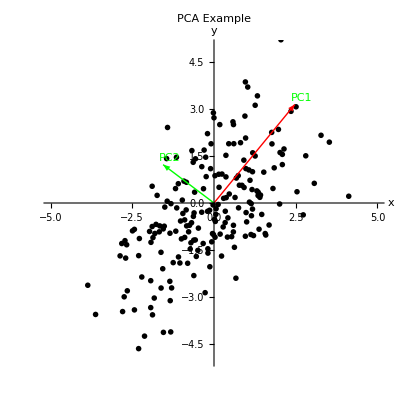

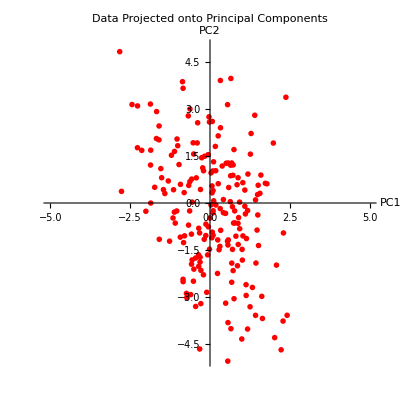

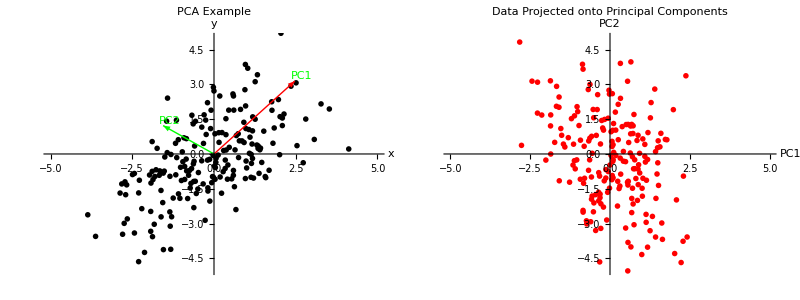

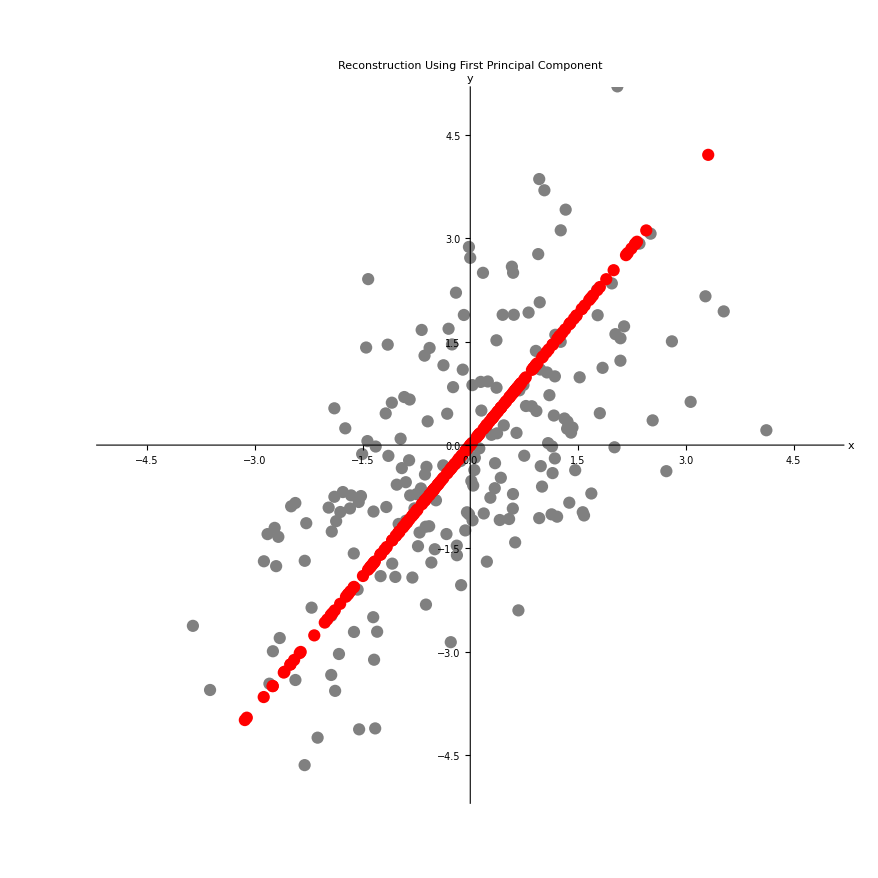

```mathematica
(*Generate sample 2D data with correlation*)
SeedRandom[42];
covMatrix={{2,1.5},{1.5,3}};
data=RandomVariate[MultinormalDistribution[{0,0},covMatrix],200];

(*Compute the sample covariance matrix*)
sampleCov=Covariance[data];
Print["Sample covariance matrix:"];
MatrixForm[sampleCov]

(*Find eigenvalues and eigenvectors of the covariance matrix*)
{pcaVals,pcaVecs}=Eigensystem[sampleCov];
Print["Eigenvalues (variances along principal components): ",pcaVals];

(*Sort eigenvalues and eigenvectors in descending order*)
indices=Ordering[pcaVals,All,Greater];
pcaVals=pcaVals[[indices]];
pcaVecs=pcaVecs[[indices]];

(*Visualize the data and principal components*)
pcaPlot=Show[ListPlot[data,PlotStyle->{Black,PointSize[0.01]},PlotLabel->"PCA Example"],(*Add arrows for principal components*)Graphics[{Red,Arrow[{{0,0},2*Sqrt[pcaVals[[1]]]*pcaVecs[[1]]}],Green,Arrow[{{0,0},2*Sqrt[pcaVals[[2]]]*pcaVecs[[2]]}],Text["PC1",2*Sqrt[pcaVals[[1]]]*pcaVecs[[1]]+{0.2,0.2}],Text["PC2",2*Sqrt[pcaVals[[2]]]*pcaVecs[[2]]+{0.2,0.2}]}],PlotRange->{{-5,5},{-5,5}},AspectRatio->1,AxesLabel->{"x","y"}]

(*Project the data onto principal components*)
projectionMatrix=Transpose[pcaVecs];
projectedData=Map[projectionMatrix.#&,data];

(*Visualize projected data*)
projectedPlot=ListPlot[projectedData,PlotStyle->{Red,PointSize[0.01]},PlotLabel->"Data Projected onto Principal Components",AxesLabel->{"PC1","PC2"},AspectRatio->1,PlotRange->{{-5,5},{-5,5}}]

(*Show both plots side by side*)
Grid[{{pcaPlot,projectedPlot}}]

(*Reconstruct data using only the first principal component*)
reconstructionPC1=Map[pcaVecs[[1]]*(pcaVecs[[1]].#)&,data];

(*Visualize reconstruction with one principal component*)
reconstructionPlot=Show[ListPlot[data,PlotStyle->{Gray,PointSize[0.01]}],ListPlot[reconstructionPC1,PlotStyle->{Red,PointSize[0.01]}],PlotLabel->"Reconstruction Using First Principal Component",AxesLabel->{"x","y"},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];

reconstructionPlot
```

### Dynamical Systems

Eigenvalues determine the stability of fixed points in dynamical systems.

(2 | 1
-2 | -1)

Eigenvalues: {1,0}

Eigenvectors:

{(-1
1),(-1
2)}

Classification of fixed point at origin: Center/neutral (at least one eigenvalue has zero real part)

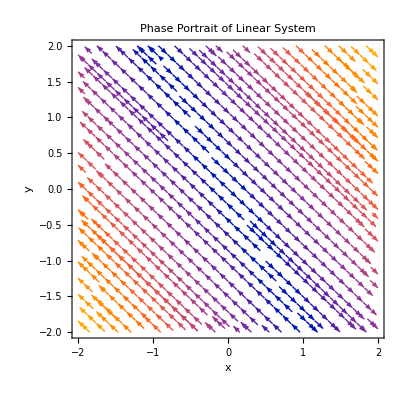

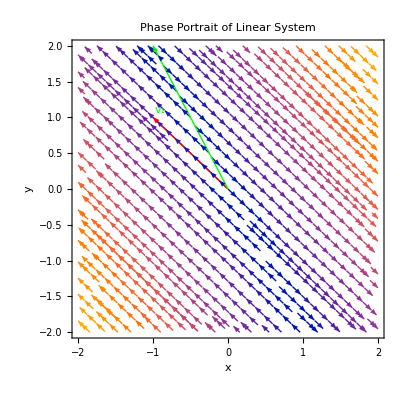

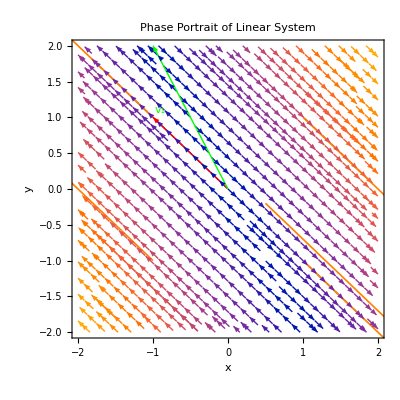

```mathematica
ClearAll[x,y]
(*Define a simple linear dynamical system:dx/dt=Ax*)
A={{2,1},{-2,-1}};
MatrixForm[A]

(*Find eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[A];
Print["Eigenvalues: ",vals];
Print["Eigenvectors: "];
Map[MatrixForm,vecs]

classification=Which[AllTrue[Re[vals],#<0&],"Stable node/spiral (all eigenvalues have negative real parts)",AllTrue[Re[vals],#>0&],"Unstable node/spiral (all eigenvalues have positive real parts)",AnyTrue[Re[vals],#==0&],"Center/neutral (at least one eigenvalue has zero real part)",True,"Saddle point (mixed positive and negative real parts)"];

Print["Classification of fixed point at origin: ",classification];


(*Define the vector field*)
vectorField[{x_,y_}]:=A.{x,y};

(*Create a stream plot of the vector field*)
streamPlot=StreamPlot[vectorField[{x,y}],{x,-2,2},{y,-2,2},StreamPoints->Fine,StreamScale->Small,StreamStyle->Blue,PlotLabel->"Phase Portrait of Linear System",AxesLabel->{"x","y"}]

(*Add eigenvectors to the plot*)
dynamicsPlot=Show[streamPlot,Graphics[{Red,Arrow[{{0,0},vecs[[1]]}],Green,Arrow[{{0,0},vecs[[2]]}],Text["v₁",vecs[[1]]+{0.1,0.1}],Text["v₂",vecs[[2]]+{0.1,0.1}]}]]

(*Solve the system for some initial conditions*)
tmax=3;
initialConditions={{1,1},{-1,1},{1,-1},{-1,-1},{0.5,-0.2}};

trajectories=Table[NDSolve[{x'[t]==A[[1,1]]*x[t]+A[[1,2]]*y[t],y'[t]==A[[2,1]]*x[t]+A[[2,2]]*y[t],x[0]==ic[[1]],y[0]==ic[[2]]},{x,y},{t,0,tmax}],{ic,initialConditions}];

(*Plot trajectories*)
trajectoriesPlot=Show[dynamicsPlot,Table[ParametricPlot[Evaluate[{x[t],y[t]}/. trajectories[[i,1]]],{t,0,tmax},PlotStyle->{Orange,Thickness[0.003]}],{i,1,Length[initialConditions]}],PlotRange->{{-2,2},{-2,2}}];

trajectoriesPlot
```

### Differential Equations - Modal Analysis

Eigenvalues and eigenvectors can be used to solve systems of differential equations.

System matrix A = -M⁻.b9K:

(-3/2 | 1/2
1/3 | -2/3)

Eigenvalues: {-5/3,-1/2}

Natural frequencies: {ⅈ √(5/3),ⅈ/(√2)}

Eigenvectors (mode shapes):

{(-3
1),(1/2
1)}

Modal matrix P:

(-3 | 1/2
1 | 1)

Diagonalized system matrix P·A·P⁻.b9:

(-13/7 | -19/21
2/7 | -13/42)

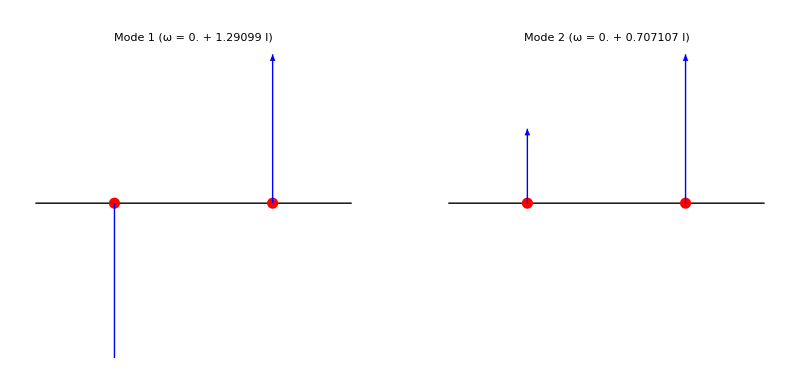

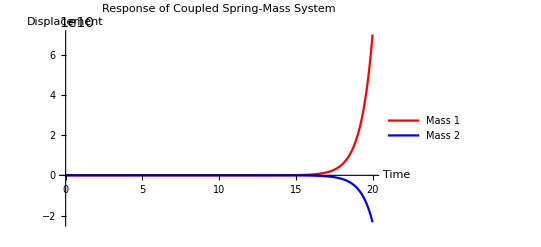

-Graphics-
-Graphics-

```mathematica
(*Consider a coupled spring-mass system modeled as d.b2x/dt.b2=Ax*)M={{2,0},{0,3}};  (*Mass matrix*)
K={{3,-1},{-1,2}};  (*Stiffness matrix*)
A=-Inverse[M].K;  (*System matrix*)

Print["System matrix A = -M⁻.b9K:"];
MatrixForm[A]

(*Find eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[A];
ω=Sqrt[vals];  (*Natural frequencies*)

Print["Eigenvalues: ",vals];
Print["Natural frequencies: ",ω];
Print["Eigenvectors (mode shapes): "];
Map[MatrixForm,vecs]

(*Modal matrix (matrix of eigenvectors)*)
P=Transpose[vecs];
Print["Modal matrix P:"];
MatrixForm[P]

(*Verify that P diagonalizes A*)
Diag=P.A.Inverse[P];
Print["Diagonalized system matrix P·A·P⁻.b9:"];
MatrixForm[Diag]

(*Visualize the mode shapes*)
modeShapePlot=GraphicsRow[Table[Graphics[{Line[{{0,0},{1,0}}],(*Base line*)Red,PointSize[0.02],Point[{0.25,0}],Point[{0.75,0}],(*Equilibrium positions*)Blue,Arrow[{{0.25,0},{0.25,vecs[[i,1]]/2}}],(*Displacement of mass 1*)Blue,Arrow[{{0.75,0},{0.75,vecs[[i,2]]/2}}]   (*Displacement of mass 2*)},PlotRange->{{0,1},{-0.5,0.5}},PlotLabel->"Mode "<>ToString[i]<>" (ω = "<>ToString[N[ω[[i]]]]<>")",AspectRatio->1],{i,1,2}]]

(*Simulate the response of the system*)
tmax=20;
x0={1,0};  (*Initial displacements*)
v0={0,0};  (*Initial velocities*)

(*Transform initial conditions to modal coordinates*)
modalIC=Inverse[P].x0;
modalVel=Inverse[P].v0;

(*Modal solution*)
modalSol[t_]:=Table[modalIC[[i]]*Cos[ω[[i]]*t]+modalVel[[i]]/ω[[i]]*Sin[ω[[i]]*t],{i,1,Length[vals]}];

(*Transform back to physical coordinates*)
physicalSol[t_]:=P.modalSol[t];

(*Plot the solution*)
responsePlot=Plot[Evaluate[physicalSol[t]],{t,0,tmax},PlotStyle->{Red,Blue},PlotLegends->{"Mass 1","Mass 2"},PlotLabel->"Response of Coupled Spring-Mass System",AxesLabel->{"Time","Displacement"},PlotRange->All]

Grid[{{modeShapePlot},{responsePlot}}]
```

### Markov Chains and the Steady State

For a stochastic matrix (transition matrix of a Markov chain), the eigenvector corresponding to eigenvalue 1 represents the steady-state probabilities.

(0.7 | 0.2 | 0.3
0.2 | 0.5 | 0.3
0.1 | 0.3 | 0.4)

Row sums: {1.2,1.,0.8}

Eigenvalues: {1.,0.441421,0.158579}

Steady-state distribution: {0.446809,0.319149,0.234043}

P·π = {0.446809,0.319149,0.234043}

π = {0.446809,0.319149,0.234043}

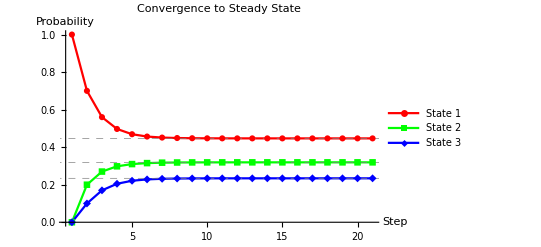

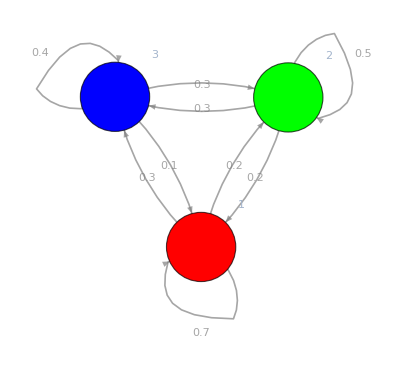

-Graphics-
-Graphics-

```mathematica
(*Define a transition matrix for a simple Markov chain*)P={{0.7,0.2,0.3},{0.2,0.5,0.3},{0.1,0.3,0.4}};
MatrixForm[P]

(*Verify that P is a stochastic matrix (rows sum to 1)*)
Print["Row sums: ",Total[P,{2}]];

(*Find eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[P];
Print["Eigenvalues: ",vals];

(*Find the index of eigenvalue closest to 1*)
idx=Ordering[Abs[vals-1],1][[1]];
steadyStateEigenvector=vecs[[idx]];

(*Normalize to get probabilities (sum to 1)*)
steadyState=steadyStateEigenvector/Total[steadyStateEigenvector];
Print["Steady-state distribution: ",steadyState];

(*Verify P·π=π,where π is the steady-state vector*)
Print["P·π = ",P.steadyState];
Print["π = ",steadyState];

(*Alternative method:iterate the transition matrix*)
initialState={1,0,0};  (*Start in state 1*)
states=NestList[P.#&,initialState,20];

(*Plot the convergence to steady state*)
steadyStatePlot=ListPlot[Transpose[states],Joined->True,PlotStyle->{Red,Green,Blue},PlotMarkers->Automatic,PlotLegends->{"State 1","State 2","State 3"},PlotLabel->"Convergence to Steady State",AxesLabel->{"Step","Probability"},PlotRange->All,GridLines->{None,{steadyState[[1]],steadyState[[2]],steadyState[[3]]}},GridLinesStyle->Directive[Gray,Dashed]]

(*Visualize the Markov chain as a graph*)
markovGraph=Graph[{1->1,1->2,1->3,2->1,2->2,2->3,3->1,3->2,3->3},EdgeWeight->Flatten[P],EdgeLabels->"EdgeWeight",VertexLabels->"Name",VertexSize->Large,VertexStyle->{1->Red,2->Green,3->Blue},EdgeStyle->Directive[Gray,Thickness[0.003]]]

Grid[{{markovGraph},{steadyStatePlot}}]
```

### Google PageRank

Random Web Graph (Adjacency Matrix):

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

PageRank transition matrix:

(0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.435 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.01 | 0.01 | 0.01 | 0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.293333 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.01 | 0.01 | 0.86 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.01 | 0.293333 | 0.01 | 0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.435
0.01 | 0.01 | 0.293333 | 0.01 | 0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.435 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.293333 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.293333 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.293333 | 0.18 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.435 | 0.01
0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.18 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.435 | 0.01
0.2225 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.86 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.86 | 0.01 | 0.01
0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.01 | 0.18 | 0.01 | 0.01 | 0.86 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01
0.2225 | 0.293333 | 0.293333 | 0.01 | 0.01 | 0.01 | 0.18 | 0.01 | 0.86 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.435
0.01 | 0.01 | 0.01 | 0.01 | 0.2225 | 0.293333 | 0.18 | 0.01 | 0.01 | 0.01 | 0.01 | 0.0666667 | 0.01 | 0.01 | 0.01)

PageRank values: {0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667}

PageRank via power iteration: {0.0574836,0.0270935,0.030668,0.0261292,0.0406626,0.0599179,0.0748136,0.0261292,0.0354295,0.0965988,0.0918373,0.149166,0.11328,0.114002,0.0567886}

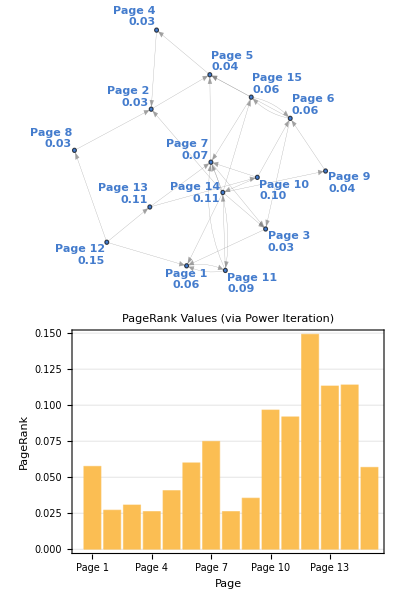

```mathematica
(*Generate a random web graph with controlled density*)
n=15;  (*Number of pages*)
linkProbability=0.2;  (*Probability of a link between any two pages*)

(*Create a random adjacency matrix with no self-loops*)
SeedRandom[42];  (*Set a seed for reproducibility*)
webGraph=Table[If[i==j,0,(*No self-loops*)If[RandomReal[]<linkProbability,1,0]],{i,1,n},{j,1,n}];

(*Ensure each page has at least one outgoing link unless it's deliberately a sink*)
sinkProbability=0.1;  (*Probability of a page being a sink*)
For[i=1,i<=n,i++,If[Total[webGraph[[i]]]==0&&RandomReal[]>sinkProbability,(*This page has no outlinks and isn't selected to be a sink-add a random link*)randomTarget=RandomInteger[{1,n}];
While[randomTarget==i,randomTarget=RandomInteger[{1,n}]];
webGraph[[i,randomTarget]]=1;]];

(*Display the random web graph matrix*)
Print["Random Web Graph (Adjacency Matrix):"];
MatrixForm[webGraph]
(*Create column-stochastic transition matrix*)
(*First,normalize columns to sum to 1*)
outDegrees=Total[webGraph,{1}];
stochasticMatrix=Table[If[outDegrees[[j]]>0,webGraph[[i,j]]/outDegrees[[j]],1/Length[webGraph]],{i,1,Length[webGraph]},{j,1,Length[webGraph]}];

(*Apply damping factor (random jump probability)*)
d=0.85;  (*Damping factor used in PageRank*)
n=Length[webGraph];
dampedMatrix=d*stochasticMatrix+(1-d)/n*ConstantArray[1,{n,n}];
Print["PageRank transition matrix:"];
MatrixForm[dampedMatrix]

(*Compute PageRank as the dominant eigenvector*)
{vals,vecs}=Eigensystem[Transpose[dampedMatrix]];
dominantIdx=Ordering[Abs[vals],1,Greater][[1]];
pageRank=vecs[[dominantIdx]];
pageRank=Abs[pageRank]/Total[Abs[pageRank]]; (*Ensure real values*)
Print["PageRank values: ",pageRank];

initialRank=ConstantArray[1/n,n];
powerIter[v_,iterations_]:=Nest[dampedMatrix.#&,v,iterations];
powerRank=powerIter[initialRank,50];
powerRank=powerRank/Total[powerRank];  (*Normalize*)
Print["PageRank via power iteration: ",powerRank];

(*Visualize the web graph with PageRank values computed from power iteration*)edgeList=Flatten[Table[If[webGraph[[i,j]]>0,i->j,Nothing],{i,1,n},{j,1,n}]];

(*Use powerRank instead of pageRank*)
pageRankGraph=Graph[edgeList,VertexSize->0.1+0.5*powerRank,VertexStyle->(ColorData["Rainbow"][#]&/@Rescale[powerRank,{Min[powerRank],Max[powerRank]},{0,1}]),VertexLabels->Table[i->Style["Page "<>ToString[i]<>"\n"<>TextString[NumberForm[powerRank[[i]],{3,2}]],Bold],{i,1,n}],EdgeStyle->Directive[Gray,Thickness[0.0003]],GraphLayout->"SpringEmbedding"];

(*Use powerRank in bar chart too*)
pageRankBarChart=BarChart[powerRank,ChartLabels->Table["Page "<>ToString[i],{i,1,n}],PlotLabel->"PageRank Values (via Power Iteration)",AxesLabel->{"Page","PageRank"},PlotTheme->"Detailed"];

Grid[{{pageRankGraph},{pageRankBarChart}},Alignment->{{Left,Right},{Top,Bottom}}]
```

## Norms, Least Squares and Approximation Methods

## Matrix Norms

Matrix norms are essential tools in numerical linear algebra that allow us to quantify the “size” of matrices. They are particularly important for analyzing errors, convergence of iterative methods, and stability of numerical algorithms.

A matrix norm  is a function that maps a matrix to a non-negative real number satisfying the following properties:

 for all matrices , and  if and only if 
 for all scalars  and matrices 
 for all matrices  and  of the same size

Let’s implement and visualize different matrix norms in Mathematica:

```mathematica
(*Define a sample matrix*)
A={{3,1,4},{1,5,9},{2,6,5}};
MatrixForm[A]

(*Frobenius Norm*)
frobeniusNorm[mat_]:=Sqrt[Total[Abs[mat]^2,2]]
frobeniusNormA=frobeniusNorm[A]
Print["Frobenius norm: ",frobeniusNormA]

(*Using built-in functions*)
Print["Built-in Frobenius norm: ",Norm[A,"Frobenius"]]

(*1-Norm (maximum column sum)*)
oneNorm[mat_]:=Max[Total[Abs[mat],{1}]]
Print["1-Norm: ",oneNorm[A]]
Print["Built-in 1-Norm: ",Norm[A,1]]

(*Infinity Norm (maximum row sum)*)
infinityNorm[mat_]:=Max[Total[Abs[mat],{2}]]
Print["Infinity Norm: ",infinityNorm[A]]
Print["Built-in Infinity Norm: ",Norm[A,Infinity]]

(*2-Norm (maximum singular value)*)
twoNorm[mat_]:=Max[SingularValueList[N[mat]]]
Print["2-Norm: ",twoNorm[A]]
Print["Built-in 2-Norm: ",Norm[A,2]]
```

(3 | 1 | 4
1 | 5 | 9
2 | 6 | 5)

3 √22

Frobenius norm: 3 √22

Built-in Frobenius norm: 3 √22

1-Norm: 18

Built-in 1-Norm: 18

Infinity Norm: 15

Built-in Infinity Norm: 15

2-Norm: 13.5824

Built-in 2-Norm: √(Root184.Root[-8100+2538 #1-198 #1^2+#1^3&,3]184.48044859407824)

### Visualizing Matrix Norms

We can visualize how different norms measure matrices by examining the unit ball in each norm:

-Graphics3D-

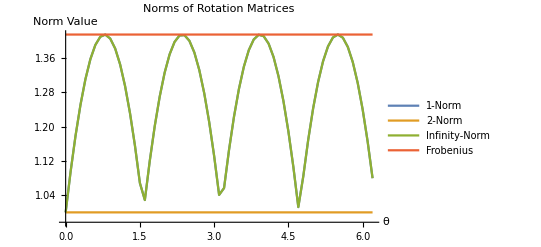

```mathematica
(*Visualize unit balls for different matrix norms in 2x2 matrices*)(*We'll parameterize 2x2 matrices using 4 parameters*)unitBallFrobenius=RegionPlot3D[a^2+b^2+c^2<=1,{a,-1,1},{b,-1,1},{c,-1,1},PlotLabel->"Frobenius Norm Unit Ball (partial view)",AxesLabel->{"a","b","c"},PlotStyle->Opacity[0.7]]

(*Creating a function to compute norm values at different points*)
normComparisonPlot=Table[With[{mat={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}},{θ,Norm[mat,1],Norm[mat,2],Norm[mat,Infinity],Norm[mat,"Frobenius"]}],{θ,0,2π,0.1}];

ListLinePlot[Transpose[{normComparisonPlot[[All,1]],#}]&/@Transpose[normComparisonPlot[[All,2;;]]],PlotLegends->{"1-Norm","2-Norm","Infinity-Norm","Frobenius"},AxesLabel->{"θ","Norm Value"},PlotLabel->"Norms of Rotation Matrices"]
```

### Equivalence of Matrix Norms

An important property of matrix norms is their equivalence . For any two matrix norms  and  , there exist positive constants  and  such that : ​

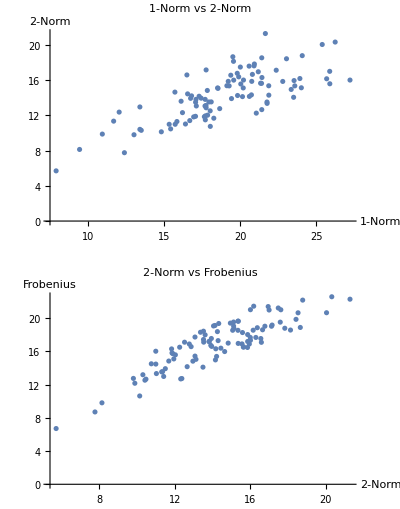

Bounds between 1-Norm and 2-Norm: {0.582063,1.02794}

Bounds between 2-Norm and Frobenius: {1.01262,1.45877}

```mathematica
(*Generate random matrices and compare norms*)
normEquivalenceData=Table[With[{mat=RandomReal[{-10,10},{3,3}]},{Norm[mat,1],Norm[mat,2],Norm[mat,Infinity],Norm[mat,"Frobenius"]}],{i,1,100}];
(*Plot relationships between different norms*)
GraphicsGrid[{{ListPlot[normEquivalenceData[[All,{1,2}]],PlotLabel->"1-Norm vs 2-Norm",AxesLabel->{"1-Norm","2-Norm"}]},{ListPlot[normEquivalenceData[[All,{2,4}]],PlotLabel->"2-Norm vs Frobenius",AxesLabel->{"2-Norm","Frobenius"}]}}]

(*Calculate bounds between norms*)
FindBounds[data_,normX_,normY_]:=Module[{ratios},ratios=data[[All,normY]]/data[[All,normX]];
{Min[ratios],Max[ratios]}]

Print["Bounds between 1-Norm and 2-Norm: ",FindBounds[normEquivalenceData,1,2]]
Print["Bounds between 2-Norm and Frobenius: ",FindBounds[normEquivalenceData,2,4]]
```

## The Least Square Problem

### Formulation of the Least Square Problem

The least squares problem is fundamental in data analysis and numerical computing. Given a matrix  and a vector , we seek a vector  that minimizes: 
,

This minimization problem arises when we have an overdetermined system (more equations than unknowns) and no exact solution exists. Instead, we seek the solution that minimizes the sum of squared errors.

The solution to the least squares problem can be derived analytically:


This formula gives the solution when  is invertible, which occurs when   has full column tank

```mathematica
(*Define a basic least squares solver*)
leastSquaresSolve[A_,b_]:=Module[{ATA,ATb},ATA=Transpose[A].A;
ATb=Transpose[A].b;
LinearSolve[ATA,ATb]]

(*Create an example overdetermined system*)
A={{1,1},{2,1},{3,1},{4,1}};
b={6,5,7,10};

(*Solve using our function*)
x=leastSquaresSolve[A,b]
Print["Our solution: ",x]

(*Using built-in function*)
builtInSolution=LeastSquares[A,b]
Print["Built-in solution: ",builtInSolution]

(*Compute the residual*)
residual=A.x-b
residualNorm=Norm[residual,2]
Print["Residual norm: ",residualNorm]
```

{7/5,7/2}

Our solution: {7/5,7/2}

{7/5,7/2}

Built-in solution: {7/5,7/2}

{-11/10,13/10,7/10,-9/10}

√(21/5)

Residual norm: √(21/5)

### Geometrical Interpretation

Geometrically, the least squares solution is the projection of the vector  onto the column space of . This means we’re finding the vector in the column space of  that’s closest to .

```mathematica
(*Visualize the least squares solution for a simple 2D case*)
A={{1,1},{2,1},{3,1}};
b={2,3,1};

(*Column space of A is a plane in 3D space*)
colA1=A[[All,1]];
colA2=A[[All,2]];

(*Calculate the least squares solution*)
x=LeastSquares[A,b];
projection=A.x;

(*Visualize*)
lsPlot=Graphics3D[{Gray,Opacity[0.5],Polygon[{{0,0,0},colA1,colA1+colA2,colA2}],
(*Column space*)
Red,Arrow[{{0,0,0},b}],
(*Original vector b*)
Blue,Arrow[{{0,0,0},projection}],
(*Projection*)
Green,Line[{b,projection}],
(*Residual vector*)
Black,PointSize[0.02],Point[{0,0,0}],Text["Origin",{0,0,0},{-1,-1}],Text["b",b,{1,1}],Text["Projection",projection,{1,0}]},PlotRange->All,Boxed->True,AxesLabel->{"x","y","z"},PlotLabel->"Least Squares as Projection"];

Show[lsPlot]
```

-Graphics3D-

### QR Decomposition for Least Squares

As talked about QR decomposition before here’s a simple implementation to check it’s relation to Least Squares

```mathematica
(*Solve least squares using QR decomposition*)
leastSquaresQR[A_,b_]:=Module[{qr,Q,R,sol},{Q,R}=QRDecomposition[A];
sol=LinearSolve[R,Q.b];sol]

(*Compare with previous methods*)
A={{1,1},{2,1},{3,1},{4,1}};
b={6,5,7,10};

xQR=leastSquaresQR[A,b]
Print["QR solution: ",xQR]
Print["Normal equation solution: ",leastSquaresSolve[A,b]]
Print["Built-in solution: ",LeastSquares[A,b]]

(*Demonstrate numerical stability*)
(*Create an ill-conditioned matrix*)
illConditioned={{1,1},{1,1.000001},{1,0.999999}};
bIll={1,1,1};

Print["Condition number: ",LinearAlgebra`MatrixConditionNumber[illConditioned]]
Print["QR solution: ",leastSquaresQR[illConditioned,bIll]]
Print["Normal equation solution: ",leastSquaresSolve[illConditioned,bIll]]
```

{7/5,7/2}

QR solution: {7/5,7/2}

Normal equation solution: {7/5,7/2}

Built-in solution: {7/5,7/2}

Condition number: LinearAlgebra`MatrixConditionNumber[{{1,1},{1,1.},{1,0.999999}}]

QR solution: {1.,0.}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{3.,3.},{3.,3.}} may contain significant numerical errors.

Normal equation solution: {1.,0.}

### Singular Value Decomposition for Least Squares

```mathematica
leastSquaresSVD[A_,b_]:=Module[{svd,U,S,V,Sinv,solution},
{U,S,V}=SingularValueDecomposition[A];
(*Create pseudoinverse of S*)
Sinv=Map[1/#&,svals]; (*Invert nonzero values*);
solution=V.Sinv.Transpose[U].b;
solution]
(*Solve our previous example*)
xSVD=leastSquaresSVD[A,b]
Print["SVD solution: ",xSVD]

(*For ill-conditioned matrix*)
svdSolution=leastSquaresSVD[illConditioned,bIll]
Print["SVD solution for ill-conditioned problem: ",svdSolution]
```

{{(13+√269)/(10 √(1+1/100 (13+√269)^2)),(13-√269)/(10 √(1+1/100 (13-√269)^2))},{1/(√(1+1/100 (13+√269)^2)),1/(√(1+1/100 (13-√269)^2))}}.svals.{(6 (1+1/10 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(5 (1+1/5 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(7 (1+3/10 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(10 (1+2/5 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2)),(6 (1+1/10 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(5 (1+1/5 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(7 (1+3/10 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(10 (1+2/5 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2)),11 √(2/7)-15/(√14),-3 √(2/35)+7 √(7/10)-5 √(10/7)}

SVD solution: {{(13+√269)/(10 √(1+1/100 (13+√269)^2)),(13-√269)/(10 √(1+1/100 (13-√269)^2))},{1/(√(1+1/100 (13+√269)^2)),1/(√(1+1/100 (13-√269)^2))}}.svals.{(6 (1+1/10 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(5 (1+1/5 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(7 (1+3/10 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2))+(10 (1+2/5 (13+√269)))/(√((1+1/10 (13+√269))^2+(1+1/5 (13+√269))^2+(1+3/10 (13+√269))^2+(1+2/5 (13+√269))^2)),(6 (1+1/10 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(5 (1+1/5 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(7 (1+3/10 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2))+(10 (1+2/5 (13-√269)))/(√((1+1/10 (13-√269))^2+(1+1/5 (13-√269))^2+(1+3/10 (13-√269))^2+(1+2/5 (13-√269))^2)),11 √(2/7)-15/(√14),-3 √(2/35)+7 √(7/10)-5 √(10/7)}

{{0.707107,-0.707107},{0.707107,0.707107}}.svals.{1.73205,-7.07107×10^-7,2.22045×10^-16}

SVD solution for ill-conditioned problem: {{0.707107,-0.707107},{0.707107,0.707107}}.svals.{1.73205,-7.07107×10^-7,2.22045×10^-16}

## Applications in Data Fitting and Signal Processing

### Calibration in Scientific Measurement

Least squares methods are widely used in scientific measurement and instrument calibration. Let’s implement a calibration procedure for a hypothetical sensor:

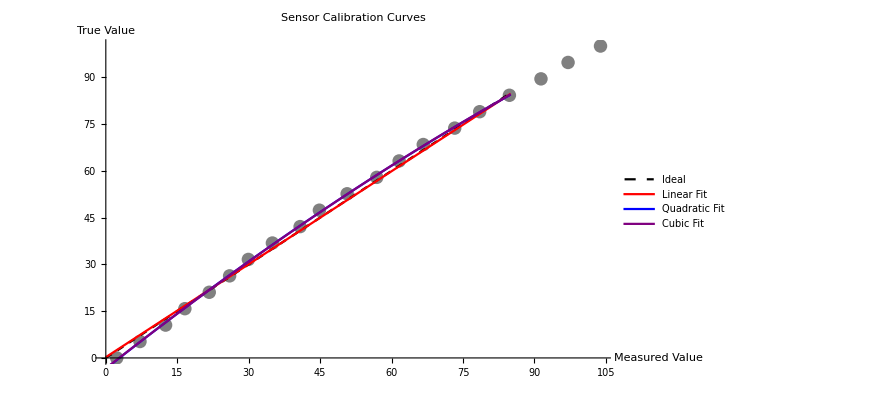

Linear model: {0.241213,0.993807}

Linear model R.b2: 0.996598

Quadratic model: {-3.44141,1.20715,-0.00203684}

Quadratic model R.b2: 0.999751

Cubic model: {-3.34771,1.19654,-0.00178423,-1.59859×10^-6}

Cubic model R.b2: 0.999753

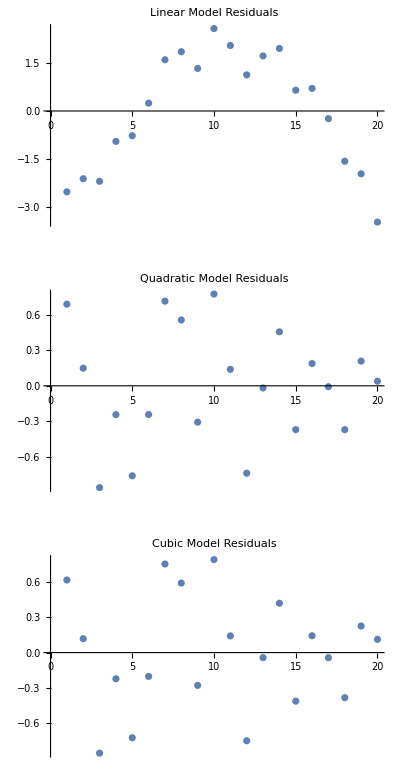

```mathematica
(*Generate calibration data with nonlinearity for n points*)generateCalibrationData[n_Integer,range_:{0,100}]:=Module[{trueValues,measuredValues,min,max},{min,max}=range;
(*Generate n evenly spaced true values*)trueValues=Subdivide[min,max,n-1];
(*Simulate a nonlinear sensor with noise*)measuredValues=0.8*trueValues+0.002*trueValues^2+3+RandomReal[{-1,1},n];
Transpose[{measuredValues,trueValues}]]

(*Example usage with 30 data points*)
calibrationData=generateCalibrationData[20];

(*Fit different calibration models*)
(*Linear model*)
linearModel=LinearModelFit[calibrationData,x,x];

(*Quadratic model*)
quadraticModel=LinearModelFit[calibrationData,{1,x,x^2},x];
(*Cubic model*)
cubicModel=LinearModelFit[calibrationData,{1,x,x^2,x^3},x];

(*Plot calibration curves*)
Show[ListPlot[calibrationData,PlotStyle->{PointSize[0.015],Gray}],Plot[{x,linearModel[x],quadraticModel[x],cubicModel[x]},{x,0,85},PlotStyle->{{Black,Dashed},Red,Blue,Purple},PlotLegends->{"Ideal","Linear Fit","Quadratic Fit","Cubic Fit"}],PlotLabel->"Sensor Calibration Curves",AxesLabel->{"Measured Value","True Value"}]

(*Evaluate the calibration models*)
Print["Linear model: ",linearModel["BestFitParameters"]]
Print["Linear model R.b2: ",linearModel["RSquared"]]
Print["Quadratic model: ",quadraticModel["BestFitParameters"]]
Print["Quadratic model R.b2: ",quadraticModel["RSquared"]]
Print["Cubic model: ",cubicModel["BestFitParameters"]]
Print["Cubic model R.b2: ",cubicModel["RSquared"]]

(*Show residuals plot*)
residualsPlot=GraphicsGrid[{{ListPlot[linearModel["FitResiduals"],PlotLabel->"Linear Model Residuals"]},{ListPlot[quadraticModel["FitResiduals"],PlotLabel->"Quadratic Model Residuals"]},{ListPlot[cubicModel["FitResiduals"],PlotLabel->"Cubic Model Residuals"]}}]
```

## Further Contents

Andreescu, Titu, D. Andrica, and D. Andrica. Complex Numbers from A To--Z. Boston: Birkhäuser, 2006.

Axler, Sheldon. Linear Algebra Done Right. Undergraduate Texts in Mathematics. Cham: Springer International Publishing, 2024. https://doi.org/10.1007/978-3-031-41026-0.

Jackson, John David. Mathematics for Quantum Mechanics: An Introductory Survey of Operators, Eigenvalues, and Linear Vector Spaces. Dover Books on Mathematics. Mineola, N.Y: Dover Publications, 2006.

Lang, Serge. Linear Algebra. Third Edition. Undergraduate Texts in Mathematics. New York, NY: Springer, 1987. https://doi.org/10.1007/978-1-4757-1949-9.